```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear will be suppressed during this calculation.

```mathematica
<<data`;
<<SVM`;
<<Matcher`;
```

```mathematica
data=nxrData[-1];
Dimensions[data]
(*data=Select[data,Length[#]≠1&];
Dimensions[data]*)
```

```mathematica
fdata=Flatten[data,{{1},{2},{3,4}}];
Dimensions[fdata]
```

{42,2,92}

```mathematica
(* 2-class based on distance*)
```

```mathematica
(*CONSTRUCTION OF INPUT X*)

(*Reap[For[i=1,i<=Length[pr],i++,
For[j=i,j≤Length[pr1],j++,
Sow[Join[pr[[i]],pr1[[j]]]]*)
(*X=Tuples[Join[pr,pr1],2]//MatrixForm;*)
(* after each op on matrix following //MatrixForm, the matrix is encapsuled in a new {}, so ,X=X[[1]]...sometimes*)
(*t2=DeleteDuplicates[Tuples[Join[pr,pr1],2],(#1===#2||#1===RotateLeft[#2])&];*)
(*{X[[Array[##+10+15&,{10}]]],
Tuples[Join[pr,pr1],2][[Array[##+10+15&,{10}]]]}//MatrixForm;*)

(*Length[t2]
X=Map[Flatten,t2,1]*)
```

```mathematica
{ddv,dsv}=eucDistV[fdata];
```

```mathematica
X=Join[add,ads];
Length[X]
X2=Join[add2,ads2];
```

83

```mathematica
(*CONSTRUCTION OF INPUT Y*)

(*t3=Table[Sign[i-8.5]*Sign[j-8.5],{i,16},{j,16}];
y=Flatten[MapIndexed[Drop[t3[[First[#2]]],First[#2]-1]&,t3]];*)
y=Join[ConstantArray[1,Length[add]],ConstantArray[-1,Length[ads]]];
Length[y]
y2=Join[ConstantArray[1,Length[add2]],ConstantArray[-1,Length[ads2]]];
```

83

```mathematica
τ=0.01;
α=SeparableSVM[X,y,τ]
```

{0,0,0.000177106,0,0,0,0,0,0.0000103304,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0000104522,0,0.0000369169,0.000212437,0,0,0.000375041,0,0,0,0,0.0000185811,0,0.000134516,0,0,0,0.000338321,0.0000679752,0,0,0,0,0.000223883,0,0,0,6.19939×10^-7,0,0,0,0,0,0.000011838,0.000294672,0.0000219504,0,0,0.000027104,0.0000230119,0,0,0,0,0,0,0.0000420642,0,0.0001545,0.000132906,0.000312964,0,0,0,0,0,0,0,2.14145×10^-7,0}

```mathematica
w=WeightVector[α,X,y];
b=Bias[α,X,y];
Length[X];
X[[SupportVectors[α]]];
yy=Map[w.##+b&,X,1]
xx=Map[w.##&,X,1]
(*DisplayTogether[ListPlot[w.X], ListPlot[Map[w.##+b&,X,1]]]*)
```

{15.9029,6.23784,0.998008,19.7092,23.1468,17.2305,17.9143,1.59394,0.998803,10.495,2.5193,5.447,16.0584,1.53069,28.5561,31.9947,17.1558,4.51127,13.6148,9.41255,14.5902,27.6685,17.7532,1.00158,3.74117,0.998428,1.00166,36.0383,36.3907,0.995358,2.25782,2.83747,14.8479,1.56619,0.992998,5.0972,1.00263,5.58768,4.52846,1.78106,0.998344,-0.998008,-1.47062,-3.76976,-1.13711,-3.44427,-0.998104,-3.564,-1.75338,-2.61802,-0.9977,-2.69423,-1.78041,-1.07415,-1.70085,-2.73547,-1.00699,-0.997182,-1.00376,-1.07411,-3.05087,-1.00433,-1.00015,-2.27008,-2.04161,-2.28538,-2.28901,-1.59065,-2.35218,-1.00707,-3.77081,-1.00038,-0.997085,-1.00671,-2.84747,-2.6066,-3.96493,-4.00776,-1.85327,-3.79677,-1.96953,-1.00707,-1.48662}

{19.1638,9.49873,4.25889,22.9701,26.4077,20.4914,21.1752,4.85483,4.25969,13.7559,5.78019,8.70789,19.3193,4.79157,31.817,35.2556,20.4167,7.77216,16.8757,12.6734,17.8511,30.9294,21.0141,4.26247,7.00205,4.25931,4.26254,39.2992,39.6516,4.25624,5.5187,6.09835,18.1088,4.82708,4.25388,8.35809,4.26352,8.84856,7.78935,5.04194,4.25923,2.26288,1.79026,-0.50887,2.12377,-0.183384,2.26278,-0.303115,1.50751,0.642868,2.26319,0.566654,1.48047,2.18673,1.56003,0.525412,2.25389,2.2637,2.25712,2.18677,0.210013,2.25656,2.26074,0.990803,1.21928,0.975506,0.971874,1.67024,0.908707,2.25381,-0.509922,2.26051,2.2638,2.25418,0.413415,0.654283,-0.704046,-0.746875,1.40761,-0.535882,1.29135,2.25381,1.77426}

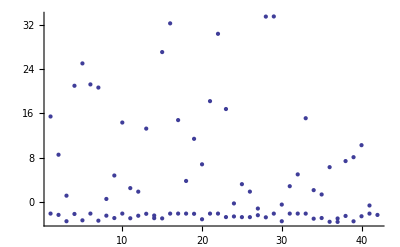

6

```mathematica
Show[ListPlot[Extract[yy,Position[y,1]]],
ListPlot[Extract[yy,Position[y,-1]]]]
syy=Sign[yy];
HammingDistance[syy,y]
(*SVMPlot[α,X,y]*)
```

```mathematica
testX=Join[tds,tdd];
Dimensions[w]
testY={-1,1,1};
yy=Map[w.##+b&,X2,1];
N[HammingDistance[Sign[Map[w.##+b&,X2,1]],y2]/Length[X2]]
```

{92}

{15.4303,8.51754,1.10799,20.9895,25.0317,21.2309,20.6636,0.515997,4.7561,14.3394,2.4752,1.83594,13.2396,-2.96181,27.0813,32.2761,14.7786,3.77102,11.3913,6.78057,18.208,30.3857,16.7805,-0.294177,3.18981,1.84163,-1.21848,33.5008,33.5239,-0.500396,2.82092,4.9575,15.1176,2.10872,1.32641,6.26519,-3.01496,7.36757,8.06986,10.2435,-0.665438,-2.12945,-2.36575,-3.51532,-2.199,-3.35258,-2.1295,-3.41244,-2.50713,-2.93945,-2.12929,-2.97756,-2.52065,-2.16752,-2.48087,-2.99818,-2.13394,-2.12903,-2.13232,-2.1675,-3.15588,-2.13261,-2.13052,-2.76548,-2.65125,-2.77313,-2.77495,-2.42577,-2.80653,-2.13398,-3.51585,-2.13063,-2.12899,-2.1338,-3.05418,-2.93374,-3.61291,-3.63432,-2.55708,-3.52883,-2.61521,-2.13398,-2.37376}

0.0722892

```mathematica
τ=0.01;
α=Timing[NonseparableSVM[X,y,0.1,τ]][[2]]
```

{0,0,0.000177116,0,0,0,0,0,0.0000103343,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0000104833,0,0.0000368823,0.000212634,0,0,0.000374993,0,0,0,0,0.0000185642,0,0.000134579,0,0,0,0.00033811,0.0000680042,0,0,0,0,0.000224172,0,0,0,6.21843×10^-7,0,0,0,0,0,0.0000117671,0.000294394,0.0000219398,0,0,0.0000271546,0.000023019,0,0,0,0,0,0,0.0000420088,0,0.000154633,0.000132826,0.000312943,0,0,0,0,0,0,0,2.13755×10^-7,0}

```mathematica
w=WeightVector[α,X,y];
b=Bias[α,X,y];
Length[X];
X[[SupportVectors[α]]];
yy=Sign[Map[w.##+b&,X,1]]
xx=Map[w.##&,X,1];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
Length[SupportVectors[α]]
```

22

```mathematica
HammingDistance[yy,y]
```

0

```mathematica
yy=Map[w.##+b&,X2,1];
N[HammingDistance[Sign[Map[w.##+b&,X2,1]],y2]/Length[X2]]
```

0.0722892

```mathematica
pk=PolynomialKernel[#1,#2,2]&;
```

```mathematica
t1=AbsoluteTime[];
α=SeparableSVM[X,y,τ,KernelFunction->pk]
t2=AbsoluteTime[];
t2-t1
```

```mathematica
(*w=WeightVector[α,X,y];
b=Bias[α,X,y,KernelFunction->pk];*)
Length[X];
(*  Sign[Total[y*α*Map[pk[#,X]&,Transpose[X]]]+b]*)

(*SVMClassify[pk,X,α,y,X[[1]]]*)
```

Thread::tdlen: Objects of unequal length in {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, « 73 »} {0, 0, 6.8661738965696`*^-11, 0, 0, 0, 0, 0, 4.2806099839905667`*^-13, 0, « 73 »} {« 1 »} cannot be combined.

Total::tllen: Lists of unequal length in {0, 0, 6.8661738965696`*^-11, 0, 0, 0, 0, 0, 4.2806099839905667`*^-13, 0, « 73 »} {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, « 73 »} {« 1 »} cannot be added.

Sign[-1.88357+Total[{0,0,6.86617×10^-11,0,0,0,0,0,4.28061×10^-13,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.39976×10^-11,3.2875×10^-11,0,0,5.78902×10^-10,0,0,0,0,5.79124×10^-12,0,1.46965×10^-10,0,0,0,2.81466×10^-10,1.76347×10^-12,1.58594×10^-11,0,0,0,2.28459×10^-10,0,0,0,0,0,0,0,0,0,0,4.1147×10^-10,2.451×10^-11,1.04395×10^-10,0,3.1311×10^-11,0,0,5.42319×10^-12,0,0,0,0,2.97316×10^-11,0,0,1.25729×10^-10,1.60435×10^-10,0,0,0,0,0,0,0,0,0} {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1} {{3.13817×10^17,3.05802×10^14,2.29664×10^16,2.94716×10^14,9.12397×10^15,2.64058×10^14,3.40141×10^15,2.4224×10^14,1.76074×10^15,2.48946×10^14,8.83481×10^14,2.20839×10^14,8.97352×10^14,1.89812×10^14,8.40399×10^14,2.24547×10^14,1.07147×10^15,2.05198×10^14,1.13587×10^15,2.02384×10^14,1.21746×10^15,2.03462×10^14,1.28599×10^15,2.07472×10^14,1.32072×10^15,2.14806×10^14,1.36989×10^15,2.17517×10^14,1.52636×10^15,2.33063×10^14,1.68199×10^15,2.05359×10^14,1.66944×10^15,2.28268×10^14,1.71824×10^15,2.23207×10^14,1.76574×10^15,2.32116×10^14,1.77585×10^15,2.5088×10^14,1.78633×10^15,2.52502×10^14,1.82041×10^15,2.57802×10^14,1.70777×10^15,3.24708×10^14,7.60672×10^14,1.08699×10^14,6.02722×10^14,1.22062×10^14,5.41219×10^14,1.44896×10^14,4.59059×10^14,1.60743×10^14,3.93393×10^14,1.66938×10^14,3.50633×10^14,1.74981×10^14,3.26227×10^14,1.84607×10^14,3.00651×10^14,1.66528×10^14,3.1466×10^14,1.60652×10^14,3.0214×10^14,1.49304×10^14,3.06552×10^14,1.37666×10^14,2.9385×10^14,1.28181×10^14,2.95589×10^14,1.23136×10^14,3.019×10^14,1.12438×10^14,2.90684×10^14,1.06526×10^14,2.8692×10^14,9.71612×10^13,2.96891×10^14,9.07037×10^13,2.86528×10^14,8.98496×10^13,2.93374×10^14,8.15123×10^13,2.92021×10^14,9.4979×10^13,2.8983×10^14,7.63666×10^13,2.83019×10^14,7.70469×10^13,3.15641×10^14,6.77188×10^13},{3.05802×10^14,1.45994×10^13,1.05031×10^14,1.35625×10^13,8.05796×10^13,1.13403×10^13,6.21301×10^13,1.1943×10^13,5.03041×10^13,1.30062×10^13,4.33094×10^13,1.50327×10^13,3.8526×10^13,1.64041×10^13,3.21121×10^13,1.728×10^13,3.38913×10^13,1.65146×10^13,3.3083×10^13,1.50191×10^13,3.34273×10^13,1.39392×10^13,3.3164×10^13,1.28889×10^13,3.24727×10^13,1.226×10^13,3.24168×10^13,1.13758×10^13,3.20688×10^13,1.08627×10^13,3.26821×10^13,9.93761×10^12,3.22633×10^13,9.45334×10^12,3.25312×10^13,9.22918×10^12,3.292×10^13,8.48196×10^12,3.3021×10^13,8.14962×10^12,3.27341×10^13,7.58484×10^12,3.32116×10^13,7.18459×10^12,3.38261×10^13,7.5318×10^12,7.23456×10^13,1.44604×10^13,6.30764×10^13,1.17846×10^13,5.60548×10^13,1.12407×10^13,4.92475×10^13,1.13048×10^13,4.341×10^13,1.29663×10^13,3.89318×10^13,1.45925×10^13,3.54947×10^13,1.64146×10^13,3.32491×10^13,1.47179×10^13,3.46012×10^13,1.39408×10^13,3.33749×10^13,1.28927×10^13,3.39355×10^13,1.20706×10^13,3.30451×10^13,1.10032×10^13,3.32495×10^13,1.0533×10^13,3.33113×10^13,1.00136×10^13,3.25689×10^13,9.1677×10^12,3.24248×10^13,8.26772×10^12,3.33488×10^13,7.76315×10^12,3.28336×10^13,7.79061×10^12,3.27788×10^13,7.41868×10^12,3.42113×10^13,6.89144×10^12,3.3576×10^13,6.36475×10^12,3.37837×10^13,6.12001×10^12,3.60456×10^13,6.12032×10^12},{2.29664×10^16,1.05031×10^14,2.86108×10^15,1.15722×10^14,1.52363×10^15,1.19348×10^14,8.39456×10^14,1.37448×10^14,5.74562×10^14,1.45967×10^14,4.19257×10^14,1.48245×10^14,3.93352×10^14,1.46947×10^14,3.44357×10^14,1.5484×10^14,3.85482×10^14,1.4558×10^14,3.84494×10^14,1.34908×10^14,3.95793×10^14,1.28311×10^14,4.00743×10^14,1.21755×10^14,3.98493×10^14,1.17779×10^14,4.02246×10^14,1.12934×10^14,4.14877×10^14,1.1122×10^14,4.33956×10^14,1.00817×10^14,4.28728×10^14,1.00807×10^14,4.35967×10^14,9.78517×10^13,4.42562×10^14,9.37442×10^13,4.42358×10^14,9.44517×10^13,4.40051×10^14,8.94789×10^13,4.45976×10^14,8.70439×10^13,4.35723×10^14,9.69436×10^13,6.06552×10^14,8.1122×10^13,5.03777×10^14,8.9414×10^13,4.3759×10^14,1.06805×10^14,3.78894×10^14,1.20281×10^14,3.34029×10^14,1.2676×10^14,3.02494×10^14,1.34327×10^14,2.79723×10^14,1.42744×10^14,2.5896×10^14,1.28452×10^14,2.69613×10^14,1.22209×10^14,2.58053×10^14,1.13453×10^14,2.61313×10^14,1.0648×10^14,2.53456×10^14,9.78598×10^13,2.53175×10^14,9.39389×10^13,2.54781×10^14,8.69382×10^13,2.45545×10^14,8.16908×10^13,2.44381×10^14,7.3981×10^13,2.50784×10^14,6.9685×10^13,2.45492×10^14,6.92882×10^13,2.46092×10^14,6.48503×10^13,2.52455×10^14,6.36931×10^13,2.47454×10^14,5.72326×10^13,2.47078×10^14,5.50553×10^13,2.6502×10^14,5.35059×10^13},{2.94716×10^14,1.35625×10^13,1.15722×10^14,1.96951×10^13,9.14009×10^13,1.88156×10^13,7.40467×10^13,1.90378×10^13,6.21143×10^13,1.89042×10^13,5.56204×10^13,1.98445×10^13,5.07937×10^13,2.00604×10^13,4.36925×10^13,2.00812×10^13,4.59464×10^13,1.88659×10^13,4.46885×10^13,1.70906×10^13,4.50296×10^13,1.59309×10^13,4.44183×10^13,1.4764×10^13,4.33136×10^13,1.38099×10^13,4.30336×10^13,1.29213×10^13,4.22586×10^13,1.23001×10^13,4.28835×10^13,1.12453×10^13,4.22865×10^13,1.07264×10^13,4.25363×10^13,1.03877×10^13,4.31392×10^13,9.58063×10^12,4.3212×10^13,9.24957×10^12,4.26334×10^13,8.7557×10^12,4.33397×10^13,7.96115×10^12,4.37857×10^13,8.61223×10^12,9.00639×10^13,1.52354×10^13,7.62274×10^13,1.82292×10^13,6.87084×10^13,1.82783×10^13,6.18855×10^13,1.75535×10^13,5.59216×10^13,1.80805×10^13,5.16913×10^13,1.88616×10^13,4.85234×10^13,1.97762×10^13,4.52732×10^13,1.77943×10^13,4.71296×10^13,1.67157×10^13,4.53723×10^13,1.54242×10^13,4.58851×10^13,1.44286×10^13,4.47826×10^13,1.32352×10^13,4.49778×10^13,1.27363×10^13,4.48677×10^13,1.17505×10^13,4.36929×10^13,1.10218×10^13,4.35354×10^13,1.00113×10^13,4.49108×10^13,9.37108×10^12,4.39973×10^13,9.43306×10^12,4.40546×10^13,8.86292×10^12,4.54092×10^13,8.34696×10^12,4.49193×10^13,7.87768×10^12,4.49763×10^13,7.39992×10^12,4.78262×10^13,7.54043×10^12},{9.12397×10^15,8.05796×10^13,1.52363×10^15,9.14009×10^13,9.22361×10^14,9.34892×10^13,5.79769×10^14,1.09985×10^14,4.28573×10^14,1.16714×10^14,3.40122×10^14,1.20988×10^14,3.14946×10^14,1.2236×10^14,2.72798×10^14,1.26727×10^14,2.97096×10^14,1.19613×10^14,2.92514×10^14,1.09812×10^14,2.98396×10^14,1.03609×10^14,2.99053×10^14,9.71298×10^13,2.94918×10^14,9.28633×10^13,2.95782×10^14,8.81341×10^13,2.99129×10^14,8.54773×10^13,3.08422×10^14,7.79425×10^13,3.04496×10^14,7.64051×10^13,3.08531×10^14,7.42082×10^13,3.12168×10^14,6.98813×10^13,3.11902×10^14,6.94799×10^13,3.09367×10^14,6.50219×10^13,3.13114×10^14,6.24664×10^13,3.09922×10^14,6.77593×10^13,5.26495×10^14,7.19946×10^13,4.44188×10^14,7.79809×10^13,3.87806×10^14,9.06191×10^13,3.38672×10^14,1.01005×10^14,3.00871×10^14,1.06241×10^14,2.73887×10^14,1.12617×10^14,2.53679×10^14,1.19756×10^14,2.35411×10^14,1.07609×10^14,2.44707×10^14,1.02128×10^14,2.34277×10^14,9.4745×10^13,2.37264×10^14,8.91538×10^13,2.30567×10^14,8.17582×10^13,2.30306×10^14,7.8435×10^13,2.31189×10^14,7.28791×10^13,2.233×10^14,6.83101×10^13,2.22592×10^14,6.17776×10^13,2.28391×10^14,5.82382×10^13,2.23852×10^14,5.8053×10^13,2.2381×10^14,5.45861×10^13,2.30477×10^14,5.24181×10^13,2.26052×10^14,4.79493×10^13,2.26525×10^14,4.58339×10^13,2.41829×10^14,4.52464×10^13},{2.64058×10^14,1.13403×10^13,1.19348×10^14,1.88156×10^13,9.34892×10^13,2.49523×10^13,7.61249×10^13,2.74204×10^13,6.55245×10^13,2.65953×10^13,6.04224×10^13,2.5774×10^13,5.69385×10^13,2.42755×10^13,5.02047×10^13,2.3122×10^13,5.29381×10^13,2.14798×10^13,5.1184×10^13,1.94393×10^13,5.14119×10^13,1.82904×10^13,5.06685×10^13,1.69043×10^13,4.93163×10^13,1.58379×10^13,4.88918×10^13,1.4946×10^13,4.76465×10^13,1.41151×10^13,4.81449×10^13,1.29938×10^13,4.74571×10^13,1.24388×10^13,4.78051×10^13,1.195×10^13,4.83493×10^13,1.11047×10^13,4.80628×10^13,1.07983×10^13,4.72546×10^13,1.00862×10^13,4.79×10^13,9.24611×10^12,4.80986×10^13,9.88583×10^12,1.01886×10^14,1.26434×10^13,8.31684×10^13,2.06915×10^13,7.30891×10^13,2.5485×10^13,6.59762×10^13,2.59831×10^13,6.09218×10^13,2.44611×10^13,5.81398×10^13,2.36782×10^13,5.57488×10^13,2.30854×10^13,5.15956×10^13,2.0927×10^13,5.38218×10^13,1.95657×10^13,5.17099×10^13,1.80611×10^13,5.20758×10^13,1.6961×10^13,5.08539×10^13,1.56652×10^13,5.08193×10^13,1.51267×10^13,5.08502×10^13,1.38946×10^13,4.90455×10^13,1.31077×10^13,4.88884×10^13,1.19599×10^13,5.01522×10^13,1.1225×10^13,4.93409×10^13,1.12192×10^13,4.93877×10^13,1.04556×10^13,5.11146×10^13,9.91841×10^12,4.99772×10^13,9.44378×10^12,4.98271×10^13,8.74729×10^12,5.29283×10^13,8.82975×10^12},{3.40141×10^15,6.21301×10^13,8.39456×10^14,7.40467×10^13,5.79769×10^14,7.61249×10^13,4.14946×10^14,8.86846×10^13,3.28854×10^14,9.28577×10^13,2.7945×10^14,9.72627×10^13,2.57065×10^14,9.92303×10^13,2.21551×10^14,1.01099×10^14,2.36495×10^14,9.56211×10^13,2.30611×10^14,8.71153×10^13,2.3352×10^14,8.17393×10^13,2.32133×10^14,7.59233×10^13,2.27511×10^14,7.19219×10^13,2.26909×10^14,6.77768×10^13,2.25777×10^14,6.48909×10^13,2.30162×10^14,5.94352×10^13,2.27051×10^14,5.7348×10^13,2.29304×10^14,5.57003×10^13,2.31487×10^14,5.17473×10^13,2.31358×10^14,5.08974×10^13,2.2899×10^14,4.74158×10^13,2.31601×10^14,4.48511×10^13,2.31785×10^14,4.77604×10^13,4.50384×10^14,6.24809×10^13,3.83434×10^14,6.8821×10^13,3.37503×10^14,7.76172×10^13,2.98889×10^14,8.45617×10^13,2.67636×10^14,8.80796×10^13,2.45597×10^14,9.28649×10^13,2.28314×10^14,9.82716×10^13,2.12159×10^14,8.82238×10^13,2.20555×10^14,8.35614×10^13,2.11372×10^14,7.74482×10^13,2.1399×10^14,7.28897×10^13,2.08361×10^14,6.67987×10^13,2.08022×10^14,6.41488×10^13,2.08559×10^14,5.96952×10^13,2.01914×10^14,5.58062×10^13,2.01367×10^14,5.04663×10^13,2.06796×10^14,4.75332×10^13,2.02689×10^14,4.75312×10^13,2.02394×10^14,4.47455×10^13,2.09029×10^14,4.2362×10^13,2.04888×10^14,3.93226×10^13,2.05857×10^14,3.73288×10^13,2.18979×10^14,3.72242×10^13},{2.4224×10^14,1.1943×10^13,1.37448×10^14,1.90378×10^13,1.09985×10^14,2.74204×10^13,8.86846×10^13,3.65613×10^13,7.5633×10^13,3.77241×10^13,7.00266×10^13,3.67237×10^13,6.52535×10^13,3.50594×10^13,5.6847×10^13,3.35617×10^13,5.93504×10^13,3.12548×10^13,5.69242×10^13,2.82972×10^13,5.70373×10^13,2.65281×10^13,5.60027×10^13,2.45745×10^13,5.42695×10^13,2.29854×10^13,5.37093×10^13,2.16869×10^13,5.19585×10^13,2.04924×10^13,5.21783×10^13,1.88827×10^13,5.13469×10^13,1.8026×10^13,5.17946×10^13,1.72502×10^13,5.21196×10^13,1.60121×10^13,5.16536×10^13,1.55927×10^13,5.04187×10^13,1.41853×10^13,5.10302×10^13,1.32749×10^13,5.10862×10^13,1.38148×10^13,1.27908×10^14,1.35345×10^13,1.02877×10^14,2.19879×10^13,8.69397×10^13,3.03086×10^13,7.6037×10^13,3.51317×10^13,6.93697×10^13,3.36768×10^13,6.53451×10^13,3.29226×10^13,6.22732×10^13,3.22787×10^13,5.73945×10^13,2.93584×10^13,5.98017×10^13,2.74582×10^13,5.72037×10^13,2.53754×10^13,5.75021×10^13,2.4012×10^13,5.60318×10^13,2.21672×10^13,5.57347×10^13,2.12621×10^13,5.58213×10^13,1.94512×10^13,5.33555×10^13,1.85657×10^13,5.33935×10^13,1.68943×10^13,5.4489×10^13,1.59486×10^13,5.37071×10^13,1.5819×10^13,5.36697×10^13,1.48169×10^13,5.54591×10^13,1.39273×10^13,5.41452×10^13,1.32024×10^13,5.38945×10^13,1.22761×10^13,5.71058×10^13,1.24379×10^13},{1.76074×10^15,5.03041×10^13,5.74562×10^14,6.21143×10^13,4.28573×10^14,6.55245×10^13,3.28854×10^14,7.5633×10^13,2.71884×10^14,7.7803×10^13,2.39932×10^14,8.04524×10^13,2.22004×10^14,8.10645×10^13,1.92456×10^14,8.10863×10^13,2.0392×10^14,7.66207×10^13,1.98004×10^14,6.9574×10^13,1.99923×10^14,6.52743×10^13,1.98002×10^14,6.02991×10^13,1.9356×10^14,5.69267×10^13,1.92649×10^14,5.35304×10^13,1.90059×10^14,5.08841×10^13,1.9272×10^14,4.67959×10^13,1.90095×10^14,4.48571×10^13,1.91699×10^14,4.35864×10^13,1.93294×10^14,4.02862×10^13,1.93228×10^14,3.95193×10^13,1.91122×10^14,3.67053×10^13,1.93237×10^14,3.4447×10^13,1.94515×10^14,3.63993×10^13,3.88312×10^14,5.26378×10^13,3.32361×10^14,6.05133×10^13,2.94334×10^14,6.8177×10^13,2.64144×10^14,7.35982×10^13,2.39179×10^14,7.46582×10^13,2.22111×10^14,7.71806×10^13,2.08257×10^14,8.02728×10^13,1.93734×10^14,7.20558×10^13,2.01425×10^14,6.81367×10^13,1.9325×10^14,6.31533×10^13,1.95648×10^14,5.94732×10^13,1.90757×10^14,5.45786×10^13,1.90501×10^14,5.2447×10^13,1.909×10^14,4.88283×10^13,1.8494×10^14,4.5652×10^13,1.84518×10^14,4.12961×10^13,1.89543×10^14,3.88711×10^13,1.85781×10^14,3.89592×10^13,1.85404×10^14,3.66544×10^13,1.91682×10^14,3.46345×10^13,1.8807×10^14,3.24526×10^13,1.89066×10^14,3.06065×10^13,2.00892×10^14,3.06095×10^13},{2.48946×10^14,1.30062×10^13,1.45967×10^14,1.89042×10^13,1.16714×10^14,2.65953×10^13,9.28577×10^13,3.77241×10^13,7.7803×10^13,4.09306×10^13,7.10437×10^13,4.09826×10^13,6.48579×10^13,4.03284×10^13,5.54056×10^13,3.93995×10^13,5.74718×10^13,3.68722×10^13,5.48913×10^13,3.34384×10^13,5.49434×10^13,3.12081×10^13,5.38294×10^13,2.89923×10^13,5.20824×10^13,2.71473×10^13,5.14877×10^13,2.55602×10^13,4.97403×10^13,2.42324×10^13,4.98795×10^13,2.22698×10^13,4.90175×10^13,2.12601×10^13,4.94399×10^13,2.03394×10^13,4.96328×10^13,1.88259×10^13,4.91779×10^13,1.83151×10^13,4.78095×10^13,1.65363×10^13,4.83853×10^13,1.56415×10^13,4.83031×10^13,1.60779×10^13,1.34666×10^14,1.4586×10^13,1.08109×10^14,2.13854×10^13,8.96857×10^13,2.99019×10^13,7.65169×10^13,3.62078×10^13,6.86387×10^13,3.62533×10^13,6.34399×10^13,3.64685×10^13,5.95798×10^13,3.67306×10^13,5.48477×10^13,3.33996×10^13,5.70892×10^13,3.13078×10^13,5.44622×10^13,2.89661×10^13,5.47544×10^13,2.74268×10^13,5.32562×10^13,2.52757×10^13,5.2956×10^13,2.4189×10^13,5.30861×10^13,2.20906×10^13,5.04814×10^13,2.11346×10^13,5.05887×10^13,1.91901×10^13,5.14826×10^13,1.81675×10^13,5.09211×10^13,1.7961×10^13,5.07901×10^13,1.68581×10^13,5.2596×10^13,1.57584×10^13,5.1183×10^13,1.48357×10^13,5.08507×10^13,1.38761×10^13,5.38917×10^13,1.41102×10^13},{8.83481×10^14,4.33094×10^13,4.19257×10^14,5.56204×10^13,3.40122×10^14,6.04224×10^13,2.7945×10^14,7.00266×10^13,2.39932×10^14,7.10437×10^13,2.19736×10^14,7.23294×10^13,2.0435×10^14,7.19346×10^13,1.78173×10^14,7.06726×10^13,1.8753×10^14,6.66553×10^13,1.81355×10^14,6.03472×10^13,1.82616×10^14,5.6607×10^13,1.80246×10^14,5.20545×10^13,1.7568×10^14,4.89374×10^13,1.74497×10^14,4.59529×10^13,1.70795×10^14,4.33645×10^13,1.72293×10^14,4.00148×10^13,1.69996×10^14,3.81182×10^13,1.71205×10^14,3.70408×10^13,1.72417×10^14,3.40474×10^13,1.72422×10^14,3.33622×10^13,1.70276×10^14,3.08455×10^13,1.72238×10^14,2.87382×10^13,1.74126×10^14,3.01213×10^13,3.57506×10^14,4.72261×10^13,3.0707×10^14,5.6937×10^13,2.73367×10^14,6.44696×10^13,2.47611×10^14,6.94972×10^13,2.26395×10^14,6.87127×10^13,2.12371×10^14,6.95739×10^13,2.00813×10^14,7.10812×10^13,1.86958×10^14,6.38046×10^13,1.94405×10^14,6.02238×10^13,1.86684×10^14,5.57981×10^13,1.88962×10^14,5.26546×10^13,1.84415×10^14,4.83365×10^13,1.84056×10^14,4.64745×10^13,1.84492×10^14,4.33222×10^13,1.78855×10^14,4.05292×10^13,1.78512×10^14,3.66422×10^13,1.83368×10^14,3.44629×10^13,1.79732×10^14,3.46434×10^13,1.79289×10^14,3.25954×10^13,1.85667×10^14,3.07298×10^13,1.82025×10^14,2.90553×10^13,1.83351×10^14,2.7263×10^13,1.94498×10^14,2.73748×10^13},{2.20839×10^14,1.50327×10^13,1.48245×10^14,1.98445×10^13,1.20988×10^14,2.5774×10^13,9.72627×10^13,3.67237×10^13,8.04524×10^13,4.09826×10^13,7.23294×10^13,4.32228×10^13,6.42038×10^13,4.43945×10^13,5.33382×10^13,4.45434×10^13,5.48659×10^13,4.20168×10^13,5.22939×10^13,3.80834×10^13,5.2204×10^13,3.53562×10^13,5.108×10^13,3.2821×10^13,4.93862×10^13,3.07433×10^13,4.87309×10^13,2.87883×10^13,4.70608×10^13,2.73458×10^13,4.71194×10^13,2.50727×10^13,4.62447×10^13,2.38356×10^13,4.66316×10^13,2.28121×10^13,4.68105×10^13,2.10293×10^13,4.63155×10^13,2.02808×10^13,4.50807×10^13,1.83619×10^13,4.55052×10^13,1.73949×10^13,4.55376×10^13,1.77618×10^13,1.42777×10^14,1.71813×10^13,1.14989×10^14,2.16107×10^13,9.4735×10^13,2.91245×10^13,7.94123×10^13,3.50505×10^13,6.9706×10^13,3.71587×10^13,6.27126×10^13,3.91514×10^13,5.75015×10^13,4.11224×10^13,5.28911×10^13,3.73215×10^13,5.50152×10^13,3.50892×10^13,5.23957×10^13,3.24753×10^13,5.27367×10^13,3.06604×10^13,5.1201×10^13,2.81567×10^13,5.09299×10^13,2.69319×10^13,5.09837×10^13,2.47105×10^13,4.85586×10^13,2.34799×10^13,4.8606×10^13,2.12933×10^13,4.94805×10^13,2.01823×10^13,4.89822×10^13,1.9911×10^13,4.87974×10^13,1.87546×10^13,5.05922×10^13,1.73482×10^13,4.91725×10^13,1.62081×10^13,4.88663×10^13,1.53003×10^13,5.17915×10^13,1.55461×10^13},{8.97352×10^14,3.8526×10^13,3.93352×10^14,5.07937×10^13,3.14946×10^14,5.69385×10^13,2.57065×10^14,6.52535×10^13,2.22004×10^14,6.48579×10^13,2.0435×10^14,6.42038×10^13,1.92812×10^14,6.22655×10^13,1.70205×10^14,6.02144×10^13,1.79954×10^14,5.6585×10^13,1.74324×10^14,5.12536×10^13,1.75738×10^14,4.82858×10^13,1.73636×10^14,4.43544×10^13,1.69359×10^14,4.17495×10^13,1.68449×10^14,3.92938×10^13,1.64961×10^14,3.70458×10^13,1.66612×10^14,3.42606×10^13,1.64515×10^14,3.27114×10^13,1.65749×10^14,3.18281×10^13,1.67016×10^14,2.93097×10^13,1.67104×10^14,2.88966×10^13,1.65089×10^14,2.67456×10^13,1.67085×10^14,2.48778×10^13,1.68822×10^14,2.62214×10^13,3.25183×10^14,4.1315×10^13,2.79638×10^14,5.28516×10^13,2.50414×10^14,6.06694×10^13,2.29253×10^14,6.53041×10^13,2.11737×10^14,6.24729×10^13,2.01031×10^14,6.1599×10^13,1.91958×10^14,6.14635×10^13,1.78817×10^14,5.51944×10^13,1.86016×10^14,5.20366×10^13,1.78804×10^14,4.82187×10^13,1.80957×10^14,4.55506×10^13,1.76706×10^14,4.18795×10^13,1.76334×10^14,4.02948×10^13,1.76882×10^14,3.7598×10^13,1.71541×10^14,3.5193×10^13,1.71205×10^14,3.18347×10^13,1.75853×10^14,2.99269×10^13,1.723×10^14,3.0131×10^13,1.71991×10^14,2.83274×10^13,1.78152×10^14,2.68766×10^13,1.74684×10^14,2.55112×10^13,1.75993×10^14,2.38319×10^13,1.86781×10^14,2.38444×10^13},{1.89812×10^14,1.64041×10^13,1.46947×10^14,2.00604×10^13,1.2236×10^14,2.42755×10^13,9.92303×10^13,3.50594×10^13,8.10645×10^13,4.03284×10^13,7.19346×10^13,4.43945×10^13,6.22655×10^13,4.74961×10^13,5.03814×10^13,4.87409×10^13,5.13828×10^13,4.62879×10^13,4.88125×10^13,4.19411×10^13,4.86025×10^13,3.87699×10^13,4.74728×10^13,3.5997×10^13,4.58593×10^13,3.37143×10^13,4.51478×10^13,3.14421×10^13,4.35691×10^13,2.99108×10^13,4.35133×10^13,2.73665×10^13,4.2623×10^13,2.59393×10^13,4.2943×10^13,2.48509×10^13,4.3068×10^13,2.28057×10^13,4.25473×10^13,2.1863×10^13,4.13966×10^13,1.9795×10^13,4.16788×10^13,1.88104×10^13,4.17656×10^13,1.90733×10^13,1.46907×10^14,1.91573×10^13,1.19001×10^14,2.10337×10^13,9.73383×10^13,2.76615×10^13,8.01274×10^13,3.33043×10^13,6.88969×10^13,3.72817×10^13,6.04606×10^13,4.08775×10^13,5.41811×10^13,4.44849×10^13,4.97692×10^13,4.03055×10^13,5.17053×10^13,3.79971×10^13,4.90958×10^13,3.51733×10^13,4.94524×10^13,3.31808×10^13,4.79439×10^13,3.03559×10^13,4.76293×10^13,2.90144×10^13,4.76526×10^13,2.66848×10^13,4.53776×10^13,2.52665×10^13,4.53821×10^13,2.28787×10^13,4.61677×10^13,2.17177×10^13,4.57406×10^13,2.13836×10^13,4.5498×10^13,2.02258×10^13,4.71954×10^13,1.84878×10^13,4.57729×10^13,1.71793×10^13,4.55388×10^13,1.63478×10^13,4.82302×10^13,1.66099×10^13},{8.40399×10^14,3.21121×10^13,3.44357×10^14,4.36925×10^13,2.72798×10^14,5.02047×10^13,2.21551×10^14,5.6847×10^13,1.92456×10^14,5.54056×10^13,1.78173×10^14,5.33382×10^13,1.70205×10^14,5.03814×10^13,1.5227×10^14,4.79679×10^13,1.61338×10^14,4.48363×10^13,1.56498×10^14,4.06234×10^13,1.57966×10^14,3.84419×10^13,1.5625×10^14,3.52929×10^13,1.525×10^14,3.32472×10^13,1.51821×10^14,3.13801×10^13,1.48831×10^14,2.95332×10^13,1.5033×10^14,2.73705×10^13,1.48581×10^14,2.6217×10^13,1.49762×10^14,2.55463×10^13,1.50956×10^14,2.35688×10^13,1.51118×10^14,2.3393×10^13,1.49289×10^14,2.16472×10^13,1.51336×10^14,2.00732×10^13,1.52892×10^14,2.13253×10^13,2.76239×10^14,3.38711×10^13,2.3777×10^14,4.60149×10^13,2.14405×10^14,5.32805×10^13,1.98368×10^14,5.71897×10^13,1.84958×10^14,5.30439×10^13,1.7753×10^14,5.09251×10^13,1.71143×10^14,4.96131×10^13,1.59716×10^14,4.46087×10^13,1.65958×10^14,4.19853×10^13,1.59694×10^14,3.88827×10^13,1.61599×10^14,3.676×10^13,1.57925×10^14,3.38743×10^13,1.57596×10^14,3.26299×10^13,1.58249×10^14,3.04343×10^13,1.53506×10^14,2.85499×10^13,1.5315×10^14,2.58282×10^13,1.57437×10^14,2.42561×10^13,1.54148×10^14,2.44899×10^13,1.53999×10^14,2.29688×10^13,1.59542×10^14,2.19713×10^13,1.56443×10^14,2.09384×10^13,1.57702×10^14,1.94681×10^13,1.67492×10^14,1.94694×10^13},{2.24547×10^14,1.728×10^13,1.5484×10^14,2.00812×10^13,1.26727×10^14,2.3122×10^13,1.01099×10^14,3.35617×10^13,8.10863×10^13,3.93995×10^13,7.06726×10^13,4.45434×10^13,6.02144×10^13,4.87409×10^13,4.79679×10^13,5.08463×10^13,4.87511×10^13,4.84171×10^13,4.62875×10^13,4.38894×10^13,4.60667×10^13,4.04819×10^13,4.5013×10^13,3.7635×10^13,4.34871×10^13,3.5275×10^13,4.27992×10^13,3.28505×10^13,4.14324×10^13,3.13218×10^13,4.13681×10^13,2.85901×10^13,4.04972×10^13,2.71104×10^13,4.0805×10^13,2.59905×10^13,4.09112×10^13,2.38278×10^13,4.04117×10^13,2.27955×10^13,3.93068×10^13,2.06596×10^13,3.95523×10^13,1.96808×10^13,3.9584×10^13,1.99348×10^13,1.46456×10^14,2.0185×10^13,1.18798×10^14,2.03712×10^13,9.67464×10^13,2.6273×10^13,7.86622×10^13,3.16199×10^13,6.66641×10^13,3.67126×10^13,5.74825×10^13,4.12954×10^13,5.0702×10^13,4.59525×10^13,4.657×10^13,4.16146×10^13,4.83082×10^13,3.92917×10^13,4.57741×10^13,3.63686×10^13,4.61319×10^13,3.42828×10^13,4.46591×10^13,3.13021×10^13,4.43393×10^13,2.99249×10^13,4.43654×10^13,2.7551×10^13,4.22377×10^13,2.60272×10^13,4.22146×10^13,2.35463×10^13,4.29562×10^13,2.23702×10^13,4.25675×10^13,2.20015×10^13,4.23173×10^13,2.08432×10^13,4.39253×10^13,1.89868×10^13,4.25005×10^13,1.75545×10^13,4.23036×10^13,1.67899×10^13,4.48279×10^13,1.70587×10^13},{1.07147×10^15,3.38913×10^13,3.85482×10^14,4.59464×10^13,2.97096×10^14,5.29381×10^13,2.36495×10^14,5.93504×10^13,2.0392×10^14,5.74718×10^13,1.8753×10^14,5.48659×10^13,1.79954×10^14,5.13828×10^13,1.61338×10^14,4.87511×10^13,1.71996×10^14,4.55585×10^13,1.67219×10^14,4.13287×10^13,1.68963×10^14,3.91842×10^13,1.6735×10^14,3.59909×10^13,1.63505×10^14,3.39603×10^13,1.62935×10^14,3.21094×10^13,1.60047×10^14,3.02613×10^13,1.62162×10^14,2.80473×10^13,1.6028×10^14,2.69171×10^13,1.61614×10^14,2.62339×10^13,1.62988×10^14,2.42861×10^13,1.63254×10^14,2.41602×10^13,1.61468×10^14,2.24559×10^13,1.63601×10^14,2.08544×10^13,1.65038×10^14,2.22501×10^13,2.8723×10^14,3.50957×10^13,2.47448×10^14,4.81653×10^13,2.23764×10^14,5.57317×10^13,2.07703×10^14,5.97081×10^13,1.94149×10^14,5.49141×10^13,1.86883×10^14,5.23953×10^13,1.80547×10^14,5.07422×10^13,1.68305×10^14,4.55687×10^13,1.75221×10^14,4.29065×10^13,1.68728×10^14,3.97572×10^13,1.7074×10^14,3.759×10^13,1.66852×10^14,3.46459×10^13,1.66537×10^14,3.33647×10^13,1.67203×10^14,3.11774×10^13,1.6231×10^14,2.9186×10^13,1.61974×10^14,2.64136×10^13,1.66429×10^14,2.47874×10^13,1.6296×10^14,2.50379×10^13,1.62826×10^14,2.34875×10^13,1.68695×10^14,2.25479×10^13,1.65423×10^14,2.1482×10^13,1.66731×10^14,1.99623×10^13,1.7706×10^14,1.98733×10^13},{2.05198×10^14,1.65146×10^13,1.4558×10^14,1.88659×10^13,1.19613×10^14,2.14798×10^13,9.56211×10^13,3.12548×10^13,7.66207×10^13,3.68722×10^13,6.66553×10^13,4.20168×10^13,5.6585×10^13,4.62879×10^13,4.48363×10^13,4.84171×10^13,4.55585×10^13,4.62184×10^13,4.32491×10^13,4.18961×10^13,4.30149×10^13,3.86223×10^13,4.20157×10^13,3.58935×10^13,4.05961×10^13,3.3648×10^13,3.99434×10^13,3.13119×10^13,3.86465×10^13,2.98551×10^13,3.8604×10^13,2.72596×10^13,3.77734×10^13,2.58213×10^13,3.80609×10^13,2.47586×10^13,3.81482×10^13,2.26843×10^13,3.76664×10^13,2.16806×10^13,3.66722×10^13,1.9659×10^13,3.68441×10^13,1.87455×10^13,3.68936×10^13,1.8956×10^13,1.39047×10^14,1.93219×10^13,1.12973×10^14,1.90292×10^13,9.18959×10^13,2.44771×10^13,7.45339×10^13,2.94661×10^13,6.29985×10^13,3.4534×10^13,5.41252×10^13,3.90945×10^13,4.756×10^13,4.37523×10^13,4.3639×10^13,3.95851×10^13,4.53102×10^13,3.74048×10^13,4.29204×10^13,3.46456×10^13,4.32713×10^13,3.26495×10^13,4.18824×10^13,2.97909×10^13,4.15845×10^13,2.84706×10^13,4.15818×10^13,2.62426×10^13,3.96058×10^13,2.47599×10^13,3.95846×10^13,2.23971×10^13,4.02563×10^13,2.12903×10^13,3.99151×10^13,2.09195×10^13,3.96555×10^13,1.98467×10^13,4.11662×10^13,1.80282×10^13,3.98433×10^13,1.66605×10^13,3.96661×10^13,1.59524×10^13,4.2012×10^13,1.61881×10^13},{1.13587×10^15,3.3083×10^13,3.84494×10^14,4.46885×10^13,2.92514×10^14,5.1184×10^13,2.30611×10^14,5.69242×10^13,1.98004×10^14,5.48913×10^13,1.81355×10^14,5.22939×10^13,1.74324×10^14,4.88125×10^13,1.56498×10^14,4.62875×10^13,1.67219×10^14,4.32491×10^13,1.62879×10^14,3.92554×10^13,1.64679×10^14,3.72494×10^13,1.63251×10^14,3.4224×10^13,1.59614×10^14,3.23201×10^13,1.59162×10^14,3.05788×10^13,1.56559×10^14,2.88345×10^13,1.58844×10^14,2.67278×10^13,1.57047×10^14,2.56731×10^13,1.58431×10^14,2.50428×10^13,1.59852×10^14,2.32157×10^13,1.6014×10^14,2.3103×10^13,1.58521×10^14,2.153×10^13,1.60675×10^14,1.99825×10^13,1.62037×10^14,2.14153×10^13,2.76058×10^14,3.39678×10^13,2.37786×10^14,4.66543×10^13,2.15527×10^14,5.36348×10^13,2.00413×10^14,5.72699×10^13,1.87455×10^14,5.25407×10^13,1.80595×10^14,5.00286×10^13,1.74639×10^14,4.84007×10^13,1.62846×10^14,4.34466×10^13,1.69611×10^14,4.09136×10^13,1.63461×10^14,3.79154×10^13,1.65399×10^14,3.58314×10^13,1.61642×10^14,3.30265×10^13,1.6142×10^14,3.1801×10^13,1.62036×10^14,2.97658×10^13,1.57431×10^14,2.78188×10^13,1.57093×10^14,2.51802×10^13,1.61454×10^14,2.36194×10^13,1.58081×10^14,2.38673×10^13,1.58007×10^14,2.23876×10^13,1.63727×10^14,2.15299×10^13,1.60611×10^14,2.04924×10^13,1.6184×10^14,1.90497×10^13,1.71935×10^14,1.894×10^13},{2.02384×10^14,1.50191×10^13,1.34908×10^14,1.70906×10^13,1.09812×10^14,1.94393×10^13,8.71153×10^13,2.82972×10^13,6.9574×10^13,3.34384×10^13,6.03472×10^13,3.80834×10^13,5.12536×10^13,4.19411×10^13,4.06234×10^13,4.38894×10^13,4.13287×10^13,4.18961×10^13,3.92554×10^13,3.80097×10^13,3.9057×10^13,3.50413×10^13,3.8166×10^13,3.25761×10^13,3.68883×10^13,3.05549×10^13,3.63025×10^13,2.84394×10^13,3.51549×10^13,2.71263×10^13,3.51476×10^13,2.47672×10^13,3.43961×10^13,2.34766×10^13,3.46652×10^13,2.25121×10^13,3.47555×10^13,2.06324×10^13,3.43301×10^13,1.97379×10^13,3.34233×10^13,1.79007×10^13,3.35868×10^13,1.70788×10^13,3.36044×10^13,1.72837×10^13,1.25694×10^14,1.74234×10^13,1.02049×10^14,1.71759×10^13,8.29742×10^13,2.21195×10^13,6.7216×10^13,2.66847×10^13,5.68101×10^13,3.12894×10^13,4.87893×10^13,3.54093×10^13,4.28722×10^13,3.96255×10^13,3.93345×10^13,3.58465×10^13,4.08419×10^13,3.38776×10^13,3.8693×10^13,3.13836×10^13,3.90161×10^13,2.95767×10^13,3.77544×10^13,2.69853×10^13,3.74862×10^13,2.5789×10^13,3.74948×10^13,2.37785×10^13,3.5712×10^13,2.24292×10^13,3.56863×10^13,2.02916×10^13,3.62835×10^13,1.92917×10^13,3.59891×10^13,1.89537×10^13,3.57512×10^13,1.7981×10^13,3.71366×10^13,1.63483×10^13,3.59147×10^13,1.51039×10^13,3.5767×10^13,1.44648×10^13,3.78906×10^13,1.46747×10^13},{1.21746×10^15,3.34273×10^13,3.95793×10^14,4.50296×10^13,2.98396×10^14,5.14119×10^13,2.3352×10^14,5.70373×10^13,1.99923×10^14,5.49434×10^13,1.82616×10^14,5.2204×10^13,1.75738×10^14,4.86025×10^13,1.57966×10^14,4.60667×10^13,1.68963×10^14,4.30149×10^13,1.64679×10^14,3.9057×10^13,1.66658×10^14,3.70794×10^13,1.65279×10^14,3.40871×10^13,1.61665×10^14,3.22127×10^13,1.6131×10^14,3.04994×10^13,1.58782×10^14,2.87683×10^13,1.61219×10^14,2.66646×10^13,1.59431×10^14,2.56423×10^13,1.60847×10^14,2.50189×10^13,1.62316×10^14,2.32136×10^13,1.62642×10^14,2.31233×10^13,1.61033×10^14,2.15523×10^13,1.63284×10^14,2.00145×10^13,1.6464×10^14,2.14899×10^13,2.76513×10^14,3.41613×10^13,2.38298×10^14,4.68691×10^13,2.16137×10^14,5.36611×10^13,2.01185×10^14,5.72676×10^13,1.88264×10^14,5.24312×10^13,1.8151×10^14,4.98496×10^13,1.75683×10^14,4.8137×10^13,1.63894×10^14,4.3217×10^13,1.70711×10^14,4.06916×10^13,1.6457×10^14,3.77124×10^13,1.6653×10^14,3.56321×10^13,1.62766×10^14,3.28542×10^13,1.62586×10^14,3.16351×10^13,1.63236×10^14,2.96011×10^13,1.58595×10^14,2.76719×10^13,1.58279×10^14,2.50493×10^13,1.627×10^14,2.34934×10^13,1.59278×10^14,2.37473×10^13,1.59227×10^14,2.22565×10^13,1.64975×10^14,2.14473×10^13,1.61906×10^14,2.04102×10^13,1.63098×10^14,1.89632×10^13,1.73311×10^14,1.88393×10^13},{2.03462×10^14,1.39392×10^13,1.28311×10^14,1.59309×10^13,1.03609×10^14,1.82904×10^13,8.17393×10^13,2.65281×10^13,6.52743×10^13,3.12081×10^13,5.6607×10^13,3.53562×10^13,4.82858×10^13,3.87699×10^13,3.84419×10^13,4.04819×10^13,3.91842×10^13,3.86223×10^13,3.72494×10^13,3.50413×10^13,3.70794×10^13,3.23539×10^13,3.62562×10^13,3.00602×10^13,3.50604×10^13,2.82086×10^13,3.45291×10^13,2.62578×10^13,3.34692×10^13,2.50598×10^13,3.3479×10^13,2.28866×10^13,3.27768×10^13,2.17053×10^13,3.30379×10^13,2.08174×10^13,3.3129×10^13,1.90929×10^13,3.27189×10^13,1.82816×10^13,3.18787×10^13,1.65854×10^13,3.20351×10^13,1.58297×10^13,3.205×10^13,1.6038×10^13,1.17058×10^14,1.60521×10^13,9.50764×10^13,1.60572×10^13,7.74016×10^13,2.08061×10^13,6.28595×10^13,2.50773×10^13,5.32746×10^13,2.91903×10^13,4.5912×10^13,3.28685×10^13,4.04614×10^13,3.66394×10^13,3.71329×10^13,3.31523×10^13,3.85447×10^13,3.13258×10^13,3.65323×10^13,2.90136×10^13,3.68413×10^13,2.7348×10^13,3.5655×10^13,2.49595×10^13,3.54048×10^13,2.38548×10^13,3.54227×10^13,2.19984×10^13,3.37393×10^13,2.07594×10^13,3.37037×10^13,1.87773×10^13,3.42673×10^13,1.78463×10^13,3.39866×10^13,1.7542×10^13,3.37674×10^13,1.66335×10^13,3.50563×10^13,1.51433×10^13,3.3925×10^13,1.39835×10^13,3.37832×10^13,1.33896×10^13,3.58005×10^13,1.35709×10^13},{1.28599×10^15,3.3164×10^13,4.00743×10^14,4.44183×10^13,2.99053×10^14,5.06685×10^13,2.32133×10^14,5.60027×10^13,1.98002×10^14,5.38294×10^13,1.80246×10^14,5.108×10^13,1.73636×10^14,4.74728×10^13,1.5625×10^14,4.5013×10^13,1.6735×10^14,4.20157×10^13,1.63251×10^14,3.8166×10^13,1.65279×10^14,3.62562×10^13,1.64089×10^14,3.33464×10^13,1.60586×10^14,3.15401×10^13,1.60275×10^14,2.98807×10^13,1.57957×10^14,2.81925×10^13,1.6049×10^14,2.61303×10^13,1.58744×10^14,2.51505×10^13,1.60194×10^14,2.4551×10^13,1.61714×10^14,2.28049×10^13,1.62033×10^14,2.27315×10^13,1.60485×10^14,2.12074×10^13,1.62774×10^14,1.97064×10^13,1.64091×10^14,2.12052×10^13,2.71694×10^14,3.36231×10^13,2.34219×10^14,4.61376×10^13,2.12609×10^14,5.27779×10^13,1.98088×10^14,5.62591×10^13,1.85394×10^14,5.14211×10^13,1.78791×10^14,4.88407×10^13,1.73123×10^14,4.7147×10^13,1.61549×10^14,4.23203×10^13,1.68265×10^14,3.98518×10^13,1.62256×10^14,3.69372×10^13,1.64195×10^14,3.48885×10^13,1.60492×10^14,3.21805×10^13,1.60319×10^14,3.0984×10^13,1.60994×10^14,2.9029×10^13,1.5649×10^14,2.70979×10^13,1.56138×10^14,2.45279×10^13,1.60534×10^14,2.29986×10^13,1.57135×10^14,2.32592×10^13,1.57127×10^14,2.17969×10^13,1.62854×10^14,2.10303×10^13,1.59736×10^14,2.0004×10^13,1.60966×10^14,1.85849×10^13,1.71067×10^14,1.84424×10^13},{2.07472×10^14,1.28889×10^13,1.21755×10^14,1.4764×10^13,9.71298×10^13,1.69043×10^13,7.59233×10^13,2.45745×10^13,6.02991×10^13,2.89923×10^13,5.20545×10^13,3.2821×10^13,4.43544×10^13,3.5997×10^13,3.52929×10^13,3.7635×10^13,3.59909×10^13,3.58935×10^13,3.4224×10^13,3.25761×10^13,3.40871×10^13,3.00602×10^13,3.33464×10^13,2.79945×10^13,3.22536×10^13,2.62662×10^13,3.17698×10^13,2.44657×10^13,3.08252×10^13,2.33677×10^13,3.08522×10^13,2.1324×10^13,3.02061×10^13,2.02435×10^13,3.04561×10^13,1.94153×10^13,3.05488×10^13,1.78115×10^13,3.01871×10^13,1.70674×10^13,2.93735×10^13,1.54882×10^13,2.95492×10^13,1.47935×10^13,2.95099×10^13,1.50118×10^13,1.07592×10^14,1.4822×10^13,8.72859×10^13,1.48023×10^13,7.09562×10^13,1.91776×10^13,5.74706×10^13,2.31618×10^13,4.86086×10^13,2.70309×10^13,4.18263×10^13,3.04631×10^13,3.68266×10^13,3.39849×10^13,3.37954×10^13,3.07618×10^13,3.50744×10^13,2.90621×10^13,3.32326×10^13,2.69154×10^13,3.35005×10^13,2.53632×10^13,3.24241×10^13,2.31511×10^13,3.21906×10^13,2.2126×10^13,3.22112×10^13,2.03757×10^13,3.06659×10^13,1.92563×10^13,3.06375×10^13,1.74204×10^13,3.11469×10^13,1.65668×10^13,3.09034×10^13,1.62732×10^13,3.07104×10^13,1.54353×10^13,3.18793×10^13,1.40557×10^13,3.08304×10^13,1.29925×10^13,3.06914×10^13,1.24343×10^13,3.25325×10^13,1.26141×10^13},{1.32072×10^15,3.24727×10^13,3.98493×10^14,4.33136×10^13,2.94918×10^14,4.93163×10^13,2.27511×10^14,5.42695×10^13,1.9356×10^14,5.20824×10^13,1.7568×10^14,4.93862×10^13,1.69359×10^14,4.58593×10^13,1.525×10^14,4.34871×10^13,1.63505×10^14,4.05961×10^13,1.59614×10^14,3.68883×10^13,1.61665×10^14,3.50604×10^13,1.60586×10^14,3.22536×10^13,1.57333×10^14,3.05243×10^13,1.57046×10^14,2.89279×10^13,1.54902×10^14,2.73032×10^13,1.57482×10^14,2.53083×10^13,1.55775×10^14,2.43767×10^13,1.5725×10^14,2.38067×10^13,1.58762×10^14,2.21384×10^13,1.59033×10^14,2.20646×10^13,1.57577×10^14,2.05985×10^13,1.5985×10^14,1.91637×10^13,1.61157×10^14,2.06487×10^13,2.63686×10^14,3.27017×10^13,2.27408×10^14,4.4794×10^13,2.06487×10^14,5.11348×10^13,1.92558×10^14,5.44236×10^13,1.80198×10^14,4.97194×10^13,1.7382×10^14,4.72002×10^13,1.68367×10^14,4.55684×10^13,1.57143×10^14,4.08967×10^13,1.63687×10^14,3.85198×10^13,1.579×10^14,3.57046×10^13,1.59805×10^14,3.37123×10^13,1.56224×10^14,3.11005×10^13,1.56083×10^14,2.99472×10^13,1.56752×10^14,2.80668×10^13,1.5239×10^14,2.61842×10^13,1.52029×10^14,2.3705×10^13,1.56323×10^14,2.22262×10^13,1.53009×10^14,2.24759×10^13,1.53026×10^14,2.10604×10^13,1.58582×10^14,2.03395×10^13,1.55593×10^14,1.934×10^13,1.56764×10^14,1.79637×10^13,1.66655×10^14,1.7798×10^13},{2.14806×10^14,1.226×10^13,1.17779×10^14,1.38099×10^13,9.28633×10^13,1.58379×10^13,7.19219×10^13,2.29854×10^13,5.69267×10^13,2.71473×10^13,4.89374×10^13,3.07433×10^13,4.17495×10^13,3.37143×10^13,3.32472×10^13,3.5275×10^13,3.39603×10^13,3.3648×10^13,3.23201×10^13,3.05549×10^13,3.22127×10^13,2.82086×10^13,3.15401×10^13,2.62662×10^13,3.05243×10^13,2.46932×10^13,3.00889×10^13,2.30041×10^13,2.92308×10^13,2.19767×10^13,2.92927×10^13,2.00544×10^13,2.86798×10^13,1.90483×10^13,2.89224×10^13,1.82741×10^13,2.90236×10^13,1.67678×10^13,2.86769×10^13,1.60859×10^13,2.79281×10^13,1.45936×10^13,2.80925×10^13,1.39598×10^13,2.80575×10^13,1.41706×10^13,1.00882×10^14,1.38773×10^13,8.18901×10^13,1.37991×10^13,6.6519×10^13,1.79399×10^13,5.38732×10^13,2.16795×10^13,4.557×10^13,2.53132×10^13,3.92106×10^13,2.85339×10^13,3.45168×10^13,3.18397×10^13,3.16809×10^13,2.88226×10^13,3.28786×10^13,2.72314×10^13,3.11604×10^13,2.52276×10^13,3.14268×10^13,2.37733×10^13,3.04093×10^13,2.17108×10^13,3.01928×10^13,2.07409×10^13,3.02328×10^13,1.91235×10^13,2.87811×10^13,1.80523×10^13,2.87425×10^13,1.63356×10^13,2.92186×10^13,1.55319×10^13,2.89966×10^13,1.52559×10^13,2.88108×10^13,1.44708×10^13,2.99349×10^13,1.31908×10^13,2.89296×10^13,1.21788×10^13,2.87983×10^13,1.16598×10^13,3.05417×10^13,1.18096×10^13},{1.36989×10^15,3.24168×10^13,4.02246×10^14,4.30336×10^13,2.95782×10^14,4.88918×10^13,2.26909×10^14,5.37093×10^13,1.92649×10^14,5.14877×10^13,1.74497×10^14,4.87309×10^13,1.68449×10^14,4.51478×10^13,1.51821×10^14,4.27992×10^13,1.62935×10^14,3.99434×10^13,1.59162×10^14,3.63025×10^13,1.6131×10^14,3.45291×10^13,1.60275×10^14,3.17698×10^13,1.57046×10^14,3.00889×10^13,1.5699×10^14,2.85159×10^13,1.54847×10^14,2.69368×10^13,1.57552×10^14,2.49724×10^13,1.55897×10^14,2.40653×10^13,1.57403×10^14,2.3517×10^13,1.58927×10^14,2.18775×10^13,1.59266×10^14,2.1831×10^13,1.57855×10^14,2.03852×10^13,1.60147×10^14,1.89675×10^13,1.61417×10^14,2.04627×10^13,2.61416×10^14,3.26429×10^13,2.25497×10^14,4.46158×10^13,2.04792×10^14,5.07167×10^13,1.91151×10^14,5.39126×10^13,1.78943×10^14,4.91548×10^13,1.72761×10^14,4.65905×10^13,1.67513×10^14,4.49095×10^13,1.56422×10^14,4.03091×10^13,1.62989×10^14,3.79642×10^13,1.57277×10^14,3.5197×10^13,1.59189×10^14,3.32371×10^13,1.55647×10^14,3.06665×10^13,1.5555×10^14,2.95219×10^13,1.56233×10^14,2.76739×10^13,1.51919×10^14,2.58119×10^13,1.5159×10^14,2.33788×10^13,1.55893×10^14,2.19185×10^13,1.52599×10^14,2.21613×10^13,1.52646×10^14,2.0761×10^13,1.58157×10^14,2.00798×10^13,1.55293×10^14,1.90756×10^13,1.56371×10^14,1.77147×10^13,1.66285×10^14,1.75379×10^13},{2.17517×10^14,1.13758×10^13,1.12934×10^14,1.29213×10^13,8.81341×10^13,1.4946×10^13,6.77768×10^13,2.16869×10^13,5.35304×10^13,2.55602×10^13,4.59529×10^13,2.87883×10^13,3.92938×10^13,3.14421×10^13,3.13801×10^13,3.28505×10^13,3.21094×10^13,3.13119×10^13,3.05788×10^13,2.84394×10^13,3.04994×10^13,2.62578×10^13,2.98807×10^13,2.44657×10^13,2.89279×10^13,2.30041×10^13,2.85159×10^13,2.1501×10^13,2.77266×10^13,2.05083×10^13,2.78058×10^13,1.87061×10^13,2.72253×10^13,1.77887×10^13,2.74608×10^13,1.7058×10^13,2.75413×10^13,1.56702×10^13,2.72244×10^13,1.50524×10^13,2.6495×10^13,1.36475×10^13,2.66749×10^13,1.3065×10^13,2.66019×10^13,1.32713×10^13,9.40376×10^13,1.28655×10^13,7.62179×10^13,1.28915×10^13,6.1935×10^13,1.68196×10^13,5.02089×10^13,2.03634×10^13,4.25348×10^13,2.36782×10^13,3.66728×10^13,2.65833×10^13,3.23457×10^13,2.95765×10^13,2.96886×10^13,2.6779×10^13,3.0821×10^13,2.52964×10^13,2.92123×10^13,2.34414×10^13,2.94542×10^13,2.21007×10^13,2.84958×10^13,2.01939×10^13,2.82873×10^13,1.92929×10^13,2.83379×10^13,1.77852×10^13,2.69579×10^13,1.67951×10^13,2.69309×10^13,1.52021×10^13,2.7373×10^13,1.44519×10^13,2.71647×10^13,1.41939×10^13,2.69837×10^13,1.34638×10^13,2.80461×10^13,1.22879×10^13,2.70847×10^13,1.13531×10^13,2.69574×10^13,1.0861×10^13,2.85959×10^13,1.10048×10^13},{1.52636×10^15,3.20688×10^13,4.14877×10^14,4.22586×10^13,2.99129×10^14,4.76465×10^13,2.25777×10^14,5.19585×10^13,1.90059×10^14,4.97403×10^13,1.70795×10^14,4.70608×10^13,1.64961×10^14,4.35691×10^13,1.48831×10^14,4.14324×10^13,1.60047×10^14,3.86465×10^13,1.56559×10^14,3.51549×10^13,1.58782×10^14,3.34692×10^13,1.57957×10^14,3.08252×10^13,1.54902×10^14,2.92308×10^13,1.54847×10^14,2.77266×10^13,1.53234×10^14,2.62333×10^13,1.56006×10^14,2.42982×10^13,1.54408×10^14,2.34765×10^13,1.55958×10^14,2.29609×10^13,1.57499×10^14,2.1394×10^13,1.57842×10^14,2.13708×10^13,1.56485×10^14,1.99929×10^13,1.58806×10^14,1.86187×10^13,1.59977×10^14,2.01813×10^13,2.53368×10^14,3.17949×10^13,2.18626×10^14,4.31857×10^13,1.98994×10^14,4.89946×10^13,1.85766×10^14,5.19882×10^13,1.73824×10^14,4.74324×10^13,1.67725×10^14,4.50249×10^13,1.62506×10^14,4.34782×10^13,1.51791×10^14,3.90196×10^13,1.58061×10^14,3.67552×10^13,1.52525×10^14,3.40616×10^13,1.54381×10^14,3.21456×10^13,1.50928×10^14,2.96613×10^13,1.5084×10^14,2.85582×10^13,1.51522×10^14,2.68009×10^13,1.47395×10^14,2.49664×10^13,1.47005×10^14,2.2607×10^13,1.51241×10^14,2.11849×10^13,1.47981×10^14,2.14386×10^13,1.48067×10^14,2.00666×10^13,1.53394×10^14,1.9467×10^13,1.50594×10^14,1.84526×10^13,1.51711×10^14,1.71663×10^13,1.61402×10^14,1.69883×10^13},{2.33063×10^14,1.08627×10^13,1.1122×10^14,1.23001×10^13,8.54773×10^13,1.41151×10^13,6.48909×10^13,2.04924×10^13,5.08841×10^13,2.42324×10^13,4.33645×10^13,2.73458×10^13,3.70458×10^13,2.99108×10^13,2.95332×10^13,3.13218×10^13,3.02613×10^13,2.98551×10^13,2.88345×10^13,2.71263×10^13,2.87683×10^13,2.50598×10^13,2.81925×10^13,2.33677×10^13,2.73032×10^13,2.19767×10^13,2.69368×10^13,2.05083×10^13,2.62333×10^13,1.96586×10^13,2.633×10^13,1.79015×10^13,2.57861×10^13,1.70301×10^13,2.60105×10^13,1.6341×10^13,2.61059×10^13,1.50055×10^13,2.58126×10^13,1.44213×10^13,2.51297×10^13,1.31034×10^13,2.52981×10^13,1.25599×10^13,2.51798×10^13,1.27663×10^13,8.8703×10^13,1.22418×10^13,7.18724×10^13,1.21282×10^13,5.83148×10^13,1.58364×10^13,4.71204×10^13,1.91705×10^13,3.98224×10^13,2.23877×10^13,3.42443×10^13,2.52328×10^13,3.01328×10^13,2.81462×10^13,2.76483×10^13,2.54774×10^13,2.86998×10^13,2.40757×10^13,2.7195×10^13,2.23151×10^13,2.74274×10^13,2.10426×10^13,2.65299×10^13,1.92224×10^13,2.63466×10^13,1.83638×10^13,2.63746×10^13,1.69079×10^13,2.50903×10^13,1.59936×10^13,2.50562×10^13,1.44739×10^13,2.54502×10^13,1.37642×10^13,2.52667×10^13,1.35108×10^13,2.51032×10^13,1.28197×10^13,2.60438×10^13,1.1704×10^13,2.51925×10^13,1.07968×10^13,2.50566×10^13,1.03385×10^13,2.65776×10^13,1.04862×10^13},{1.68199×10^15,3.26821×10^13,4.33956×10^14,4.28835×10^13,3.08422×10^14,4.81449×10^13,2.30162×10^14,5.21783×10^13,1.9272×10^14,4.98795×10^13,1.72293×10^14,4.71194×10^13,1.66612×10^14,4.35133×10^13,1.5033×10^14,4.13681×10^13,1.62162×10^14,3.8604×10^13,1.58844×10^14,3.51476×10^13,1.61219×10^14,3.3479×10^13,1.6049×10^14,3.08522×10^13,1.57482×10^14,2.92927×10^13,1.57552×10^14,2.78058×10^13,1.56006×10^14,2.633×10^13,1.5923×10^14,2.43877×10^13,1.57591×10^14,2.35813×10^13,1.59191×10^14,2.30576×10^13,1.6085×10^14,2.1519×10^13,1.61247×10^14,2.15221×10^13,1.59996×10^14,2.01919×10^13,1.62345×10^14,1.88189×10^13,1.63404×10^14,2.04487×10^13,2.54359×10^14,3.2124×10^13,2.1949×10^14,4.36402×10^13,1.99924×10^14,4.91903×10^13,1.86856×10^14,5.20982×10^13,1.74905×10^14,4.7468×10^13,1.68814×10^14,4.50184×10^13,1.63692×10^14,4.34254×10^13,1.52822×10^14,3.8944×10^13,1.59358×10^14,3.67026×10^13,1.53875×10^14,3.40304×10^13,1.55759×10^14,3.21039×10^13,1.52254×10^14,2.96306×10^13,1.52214×10^14,2.85195×10^13,1.52896×10^14,2.67859×10^13,1.48808×10^14,2.49248×10^13,1.48455×10^14,2.25721×10^13,1.52725×10^14,2.11412×10^13,1.49427×10^14,2.13957×10^13,1.49519×10^14,2.00304×10^13,1.54936×10^14,1.94656×10^13,1.52136×10^14,1.84302×10^13,1.53207×10^14,1.71486×10^13,1.6297×10^14,1.69156×10^13},{2.05359×10^14,9.93761×10^12,1.00817×10^14,1.12453×10^13,7.79425×10^13,1.29938×10^13,5.94352×10^13,1.88827×10^13,4.67959×10^13,2.22698×10^13,4.00148×10^13,2.50727×10^13,3.42606×10^13,2.73665×10^13,2.73705×10^13,2.85901×10^13,2.80473×10^13,2.72596×10^13,2.67278×10^13,2.47672×10^13,2.66646×10^13,2.28866×10^13,2.61303×10^13,2.1324×10^13,2.53083×10^13,2.00544×10^13,2.49724×10^13,1.87061×10^13,2.42982×10^13,1.79015×10^13,2.43877×10^13,1.63349×10^13,2.38826×10^13,1.5536×10^13,2.40966×10^13,1.49039×10^13,2.41837×10^13,1.36939×10^13,2.39065×10^13,1.31605×10^13,2.32915×10^13,1.1949×10^13,2.34254×10^13,1.14434×10^13,2.33519×10^13,1.16366×10^13,8.18624×10^13,1.1146×10^13,6.63658×10^13,1.11813×10^13,5.38733×10^13,1.46497×10^13,4.36375×10^13,1.775×10^13,3.69652×10^13,2.06321×10^13,3.18737×10^13,2.31672×10^13,2.81141×10^13,2.57723×10^13,2.57985×10^13,2.33313×10^13,2.67832×10^13,2.20441×10^13,2.53863×10^13,2.04333×10^13,2.56022×10^13,1.92629×10^13,2.47778×10^13,1.7599×10^13,2.46087×10^13,1.68124×10^13,2.46307×10^13,1.54827×10^13,2.34372×10^13,1.46358×10^13,2.34124×10^13,1.3249×10^13,2.3788×10^13,1.26008×10^13,2.36153×10^13,1.23701×10^13,2.34662×10^13,1.17308×10^13,2.43485×10^13,1.07107×10^13,2.35633×10^13,9.88623×10^12,2.34329×10^13,9.46089×10^12,2.48565×10^13,9.58184×10^12},{1.66944×10^15,3.22633×10^13,4.28728×10^14,4.22865×10^13,3.04496×10^14,4.74571×10^13,2.27051×10^14,5.13469×10^13,1.90095×10^14,4.90175×10^13,1.69996×10^14,4.62447×10^13,1.64515×10^14,4.2623×10^13,1.48581×10^14,4.04972×10^13,1.6028×10^14,3.77734×10^13,1.57047×10^14,3.43961×10^13,1.59431×10^14,3.27768×10^13,1.58744×10^14,3.02061×10^13,1.55775×10^14,2.86798×10^13,1.55897×10^14,2.72253×10^13,1.54408×10^14,2.57861×10^13,1.57591×10^14,2.38826×10^13,1.56075×10^14,2.30983×10^13,1.57655×10^14,2.26004×10^13,1.59317×10^14,2.10893×10^13,1.59747×10^14,2.1099×10^13,1.58495×10^14,1.98006×10^13,1.60896×10^14,1.84584×10^13,1.61979×10^14,2.00667×10^13,2.50429×10^14,3.17144×10^13,2.16068×10^14,4.31997×10^13,1.97011×10^14,4.85249×10^13,1.84279×10^14,5.1345×10^13,1.72573×10^14,4.66909×10^13,1.66666×10^14,4.42139×10^13,1.61732×10^14,4.26024×10^13,1.51072×10^14,3.82061×10^13,1.57503×10^14,3.60069×10^13,1.52129×10^14,3.33735×10^13,1.54016×10^14,3.14903×10^13,1.5056×10^14,2.90572×10^13,1.50538×10^14,2.79726×10^13,1.51238×10^14,2.62943×10^13,1.47267×10^14,2.44555×10^13,1.46884×10^14,2.21433×10^13,1.51133×10^14,2.07392×10^13,1.47878×10^14,2.09964×10^13,1.47985×10^14,1.96554×10^13,1.53378×10^14,1.91235×10^13,1.50611×10^14,1.81061×10^13,1.51727×10^14,1.68418×10^13,1.61403×10^14,1.66175×10^13},{2.28268×10^14,9.45334×10^12,1.00807×10^14,1.07264×10^13,7.64051×10^13,1.24388×10^13,5.7348×10^13,1.8026×10^13,4.48571×10^13,2.12601×10^13,3.81182×10^13,2.38356×10^13,3.27114×10^13,2.59393×10^13,2.6217×10^13,2.71104×10^13,2.69171×10^13,2.58213×10^13,2.56731×10^13,2.34766×10^13,2.56423×10^13,2.17053×10^13,2.51505×10^13,2.02435×10^13,2.43767×10^13,1.90483×10^13,2.40653×10^13,1.77887×10^13,2.34765×10^13,1.70301×10^13,2.35813×10^13,1.5536×10^13,2.30983×10^13,1.48208×10^13,2.33145×10^13,1.42095×10^13,2.33927×10^13,1.30759×10^13,2.3129×10^13,1.25911×10^13,2.25287×10^13,1.143×10^13,2.26735×10^13,1.09498×10^13,2.2567×10^13,1.1167×10^13,7.73705×10^13,1.04758×10^13,6.26545×10^13,1.05791×10^13,5.08446×10^13,1.39213×10^13,4.11452×10^13,1.6881×10^13,3.48715×10^13,1.95872×10^13,3.00937×10^13,2.19415×10^13,2.65674×10^13,2.43598×10^13,2.4387×10^13,2.20642×10^13,2.53×10^13,2.08469×10^13,2.39701×10^13,1.9321×10^13,2.41704×10^13,1.82155×10^13,2.33891×10^13,1.66445×10^13,2.32298×10^13,1.59059×10^13,2.32604×10^13,1.46341×10^13,2.21103×10^13,1.38494×10^13,2.20846×10^13,1.25383×10^13,2.24395×10^13,1.19296×10^13,2.22782×10^13,1.17059×10^13,2.21398×10^13,1.10965×10^13,2.29662×10^13,1.01526×10^13,2.22251×10^13,9.36503×10^12,2.20849×10^13,8.96025×10^12,2.34494×10^13,9.07521×10^12},{1.71824×10^15,3.25312×10^13,4.35967×10^14,4.25363×10^13,3.08531×10^14,4.78051×10^13,2.29304×10^14,5.17946×10^13,1.91699×10^14,4.94399×10^13,1.71205×10^14,4.66316×10^13,1.65749×10^14,4.2943×10^13,1.49762×10^14,4.0805×10^13,1.61614×10^14,3.80609×10^13,1.58431×10^14,3.46652×10^13,1.60847×10^14,3.30379×10^13,1.60194×10^14,3.04561×10^13,1.5725×10^14,2.89224×10^13,1.57403×10^14,2.74608×10^13,1.55958×10^14,2.60105×10^13,1.59191×10^14,2.40966×10^13,1.57655×10^14,2.33145×10^13,1.59352×10^14,2.28212×10^13,1.61012×10^14,2.13007×10^13,1.61417×10^14,2.13155×10^13,1.60178×10^14,1.99968×10^13,1.62609×10^14,1.86465×10^13,1.63683×10^14,2.0297×10^13,2.5211×10^14,3.18742×10^13,2.17363×10^14,4.34206×10^13,1.98155×10^14,4.88794×10^13,1.85309×10^14,5.17937×10^13,1.73522×10^14,4.7092×10^13,1.67617×10^14,4.45553×10^13,1.62692×10^14,4.29354×10^13,1.51995×10^14,3.8511×10^13,1.58451×10^14,3.62913×10^13,1.53087×10^14,3.36422×10^13,1.54963×10^14,3.17383×10^13,1.5149×10^14,2.92854×10^13,1.51483×10^14,2.81947×10^13,1.52182×10^14,2.65145×10^13,1.482×10^14,2.46553×10^13,1.47821×10^14,2.23293×10^13,1.52109×10^14,2.09181×10^13,1.48844×10^14,2.11669×10^13,1.48984×10^14,1.9816×10^13,1.54417×10^14,1.92938×10^13,1.51647×10^14,1.82529×10^13,1.5272×10^14,1.69885×10^13,1.62525×10^14,1.67585×10^13},{2.23207×10^14,9.22918×10^12,9.78517×10^13,1.03877×10^13,7.42082×10^13,1.195×10^13,5.57003×10^13,1.72502×10^13,4.35864×10^13,2.03394×10^13,3.70408×10^13,2.28121×10^13,3.18281×10^13,2.48509×10^13,2.55463×10^13,2.59905×10^13,2.62339×10^13,2.47586×10^13,2.50428×10^13,2.25121×10^13,2.50189×10^13,2.08174×10^13,2.4551×10^13,1.94153×10^13,2.38067×10^13,1.82741×10^13,2.3517×10^13,1.7058×10^13,2.29609×10^13,1.6341×10^13,2.30576×10^13,1.49039×10^13,2.26004×10^13,1.42095×10^13,2.28212×10^13,1.36673×10^13,2.29005×10^13,1.25498×10^13,2.26468×10^13,1.20867×10^13,2.20719×10^13,1.09673×10^13,2.22306×10^13,1.05143×10^13,2.21321×10^13,1.07296×10^13,7.46744×10^13,1.01781×10^13,6.0585×10^13,1.01722×10^13,4.92858×10^13,1.3325×10^13,3.99388×10^13,1.61458×10^13,3.38565×10^13,1.8749×10^13,2.92443×10^13,2.10021×10^13,2.58344×10^13,2.33577×10^13,2.37422×10^13,2.11481×10^13,2.46045×10^13,1.99855×10^13,2.33245×10^13,1.85236×10^13,2.35238×10^13,1.74716×10^13,2.27694×10^13,1.59599×10^13,2.26217×10^13,1.52558×10^13,2.26537×10^13,1.40463×10^13,2.15535×10^13,1.32843×10^13,2.15202×10^13,1.20264×10^13,2.18735×10^13,1.14433×10^13,2.17209×10^13,1.12322×10^13,2.15998×10^13,1.06474×10^13,2.23891×10^13,9.74858×10^12,2.16874×10^13,8.98745×10^12,2.15618×10^13,8.60423×10^12,2.29075×10^13,8.72428×10^12},{1.76574×10^15,3.292×10^13,4.42562×10^14,4.31392×10^13,3.12168×10^14,4.83493×10^13,2.31487×10^14,5.21196×10^13,1.93294×10^14,4.96328×10^13,1.72417×10^14,4.68105×10^13,1.67016×10^14,4.3068×10^13,1.50956×10^14,4.09112×10^13,1.62988×10^14,3.81482×10^13,1.59852×10^14,3.47555×10^13,1.62316×10^14,3.3129×10^13,1.61714×10^14,3.05488×10^13,1.58762×10^14,2.90236×10^13,1.58927×10^14,2.75413×10^13,1.57499×10^14,2.61059×10^13,1.6085×10^14,2.41837×10^13,1.59317×10^14,2.33927×10^13,1.61012×10^14,2.29005×10^13,1.62943×10^14,2.1372×10^13,1.63304×10^14,2.13905×10^13,1.62066×10^14,2.01042×10^13,1.64558×10^14,1.87382×10^13,1.65627×10^14,2.04255×10^13,2.53849×10^14,3.21229×10^13,2.18713×10^14,4.41018×10^13,1.99576×10^14,4.94734×10^13,1.86723×10^14,5.22389×10^13,1.74884×10^14,4.74494×10^13,1.68935×10^14,4.48718×10^13,1.64034×10^14,4.32302×10^13,1.53254×10^14,3.87622×10^13,1.59766×10^14,3.65311×10^13,1.5437×10^14,3.38669×10^13,1.56254×10^14,3.19347×10^13,1.52774×10^14,2.94587×10^13,1.52781×10^14,2.8364×10^13,1.53491×10^14,2.66734×10^13,1.49541×10^14,2.48015×10^13,1.49124×10^14,2.24611×10^13,1.53461×10^14,2.10298×10^13,1.50169×10^14,2.12958×10^13,1.5035×10^14,1.9939×10^13,1.55882×10^14,1.94113×10^13,1.53026×10^14,1.83763×10^13,1.54185×10^14,1.70843×10^13,1.64069×10^14,1.6859×10^13},{2.32116×10^14,8.48196×10^12,9.37442×10^13,9.58063×10^12,6.98813×10^13,1.11047×10^13,5.17473×10^13,1.60121×10^13,4.02862×10^13,1.88259×10^13,3.40474×10^13,2.10293×10^13,2.93097×10^13,2.28057×10^13,2.35688×10^13,2.38278×10^13,2.42861×10^13,2.26843×10^13,2.32157×10^13,2.06324×10^13,2.32136×10^13,1.90929×10^13,2.28049×10^13,1.78115×10^13,2.21384×10^13,1.67678×10^13,2.18775×10^13,1.56702×10^13,2.1394×10^13,1.50055×10^13,2.1519×10^13,1.36939×10^13,2.10893×10^13,1.30759×10^13,2.13007×10^13,1.25498×10^13,2.1372×10^13,1.1597×10^13,2.11405×10^13,1.1145×10^13,2.06145×10^13,1.01272×10^13,2.07534×10^13,9.71462×10^12,2.06562×10^13,9.93266×10^12,6.86648×10^13,9.30882×10^12,5.54967×10^13,9.40775×10^12,4.50692×10^13,1.23736×10^13,3.65626×10^13,1.50107×10^13,3.10115×10^13,1.73406×10^13,2.6803×10^13,1.93638×10^13,2.37144×10^13,2.1471×10^13,2.17786×10^13,1.94409×10^13,2.25915×10^13,1.83748×10^13,2.14189×10^13,1.70243×10^13,2.16073×10^13,1.60529×10^13,2.09106×10^13,1.46679×10^13,2.07831×10^13,1.4015×10^13,2.0805×10^13,1.2904×10^13,1.97837×10^13,1.21998×10^13,1.97663×10^13,1.1042×10^13,2.00969×10^13,1.05058×10^13,1.99468×10^13,1.03158×10^13,1.98356×10^13,9.77115×10^12,2.05687×10^13,8.95769×10^12,1.9909×10^13,8.26074×10^12,1.97786×10^13,7.8984×10^12,2.10136×10^13,7.98306×10^12},{1.77585×10^15,3.3021×10^13,4.42358×10^14,4.3212×10^13,3.11902×10^14,4.80628×10^13,2.31358×10^14,5.16536×10^13,1.93228×10^14,4.91779×10^13,1.72422×10^14,4.63155×10^13,1.67104×10^14,4.25473×10^13,1.51118×10^14,4.04117×10^13,1.63254×10^14,3.76664×10^13,1.6014×10^14,3.43301×10^13,1.62642×10^14,3.27189×10^13,1.62033×10^14,3.01871×10^13,1.59033×10^14,2.86769×10^13,1.59266×10^14,2.72244×10^13,1.57842×10^14,2.58126×10^13,1.61247×10^14,2.39065×10^13,1.59747×10^14,2.3129×10^13,1.61417×10^14,2.26468×10^13,1.63304×10^14,2.11405×10^13,1.63946×10^14,2.1183×10^13,1.62604×10^14,1.9932×10^13,1.65141×10^14,1.85642×10^13,1.66174×10^14,2.02432×10^13,2.52975×10^14,3.23999×10^13,2.18047×10^14,4.41377×10^13,1.993×10^14,4.91278×10^13,1.86748×10^14,5.18316×10^13,1.75007×10^14,4.70399×10^13,1.69176×10^14,4.44431×10^13,1.64362×10^14,4.27634×10^13,1.5362×10^14,3.83454×10^13,1.60169×10^14,3.61322×10^13,1.54789×10^14,3.34939×10^13,1.5671×10^14,3.15852×10^13,1.53218×10^14,2.91398×10^13,1.53226×10^14,2.80567×10^13,1.53967×10^14,2.63789×10^13,1.50064×10^14,2.45252×10^13,1.49658×10^14,2.2219×10^13,1.54045×10^14,2.08012×10^13,1.5073×10^14,2.10713×10^13,1.50917×10^14,1.97175×10^13,1.56482×10^14,1.92405×10^13,1.53604×10^14,1.8216×10^13,1.54826×10^14,1.69307×10^13,1.64728×10^14,1.67078×10^13},{2.5088×10^14,8.14962×10^12,9.44517×10^13,9.24957×10^12,6.94799×10^13,1.07983×10^13,5.08974×10^13,1.55927×10^13,3.95193×10^13,1.83151×10^13,3.33622×10^13,2.02808×10^13,2.88966×10^13,2.1863×10^13,2.3393×10^13,2.27955×10^13,2.41602×10^13,2.16806×10^13,2.3103×10^13,1.97379×10^13,2.31233×10^13,1.82816×10^13,2.27315×10^13,1.70674×10^13,2.20646×10^13,1.60859×10^13,2.1831×10^13,1.50524×10^13,2.13708×10^13,1.44213×10^13,2.15221×10^13,1.31605×10^13,2.1099×10^13,1.25911×10^13,2.13155×10^13,1.20867×10^13,2.13905×10^13,1.1145×10^13,2.1183×10^13,1.08006×10^13,2.06409×10^13,9.7904×10^12,2.07902×10^13,9.39979×10^12,2.06576×10^13,9.61719×10^12,6.62389×10^13,8.77692×10^12,5.36785×10^13,9.07352×10^12,4.36833×10^13,1.20271×10^13,3.54737×10^13,1.46539×10^13,3.02089×10^13,1.67935×10^13,2.62437×10^13,1.86232×10^13,2.3318×10^13,2.0513×10^13,2.14243×10^13,1.85825×10^13,2.22197×10^13,1.75561×10^13,2.10617×10^13,1.62728×10^13,2.12451×10^13,1.53474×10^13,2.05585×10^13,1.4039×10^13,2.04239×10^13,1.34156×10^13,2.04796×10^13,1.23429×10^13,1.9456×10^13,1.16868×10^13,1.94423×10^13,1.05824×10^13,1.97559×10^13,1.00713×10^13,1.96158×10^13,9.88458×10^12,1.95092×10^13,9.36404×10^12,2.02486×10^13,8.61198×10^12,1.95759×10^13,7.94475×10^12,1.94594×10^13,7.59087×10^12,2.06833×10^13,7.67541×10^12},{1.78633×10^15,3.27341×10^13,4.40051×10^14,4.26334×10^13,3.09367×10^14,4.72546×10^13,2.2899×10^14,5.04187×10^13,1.91122×10^14,4.78095×10^13,1.70276×10^14,4.50807×10^13,1.65089×10^14,4.13966×10^13,1.49289×10^14,3.93068×10^13,1.61468×10^14,3.66722×10^13,1.58521×10^14,3.34233×10^13,1.61033×10^14,3.18787×10^13,1.60485×10^14,2.93735×10^13,1.57577×10^14,2.79281×10^13,1.57855×10^14,2.6495×10^13,1.56485×10^14,2.51297×10^13,1.59996×10^14,2.32915×10^13,1.58495×10^14,2.25287×10^13,1.60178×10^14,2.20719×10^13,1.62066×10^14,2.06145×10^13,1.62604×10^14,2.06409×10^13,1.61622×10^14,1.9471×10^13,1.64031×10^14,1.81072×10^13,1.65122×10^14,1.9799×10^13,2.49384×10^14,3.19048×10^13,2.15106×10^14,4.34018×10^13,1.96761×10^14,4.81317×10^13,1.84585×10^14,5.05556×10^13,1.73061×10^14,4.5859×10^13,1.67251×10^14,4.33382×10^13,1.62492×10^14,4.17471×10^13,1.51854×10^14,3.74×10^13,1.58406×10^14,3.52576×10^13,1.53194×10^14,3.27063×10^13,1.55143×10^14,3.08239×10^13,1.51693×10^14,2.84415×10^13,1.51791×10^14,2.73808×10^13,1.5243×10^14,2.57818×10^13,1.48648×10^14,2.39262×10^13,1.48238×10^14,2.16742×10^13,1.52605×10^14,2.02862×10^13,1.49305×10^14,2.05593×10^13,1.49469×10^14,1.92361×10^13,1.54941×10^14,1.87689×10^13,1.52237×10^14,1.7759×10^13,1.53385×10^14,1.65034×10^13,1.63213×10^14,1.62418×10^13},{2.52502×10^14,7.58484×10^12,8.94789×10^13,8.7557×10^12,6.50219×10^13,1.00862×10^13,4.74158×10^13,1.41853×10^13,3.67053×10^13,1.65363×10^13,3.08455×10^13,1.83619×10^13,2.67456×10^13,1.9795×10^13,2.16472×10^13,2.06596×10^13,2.24559×10^13,1.9659×10^13,2.153×10^13,1.79007×10^13,2.15523×10^13,1.65854×10^13,2.12074×10^13,1.54882×10^13,2.05985×10^13,1.45936×10^13,2.03852×10^13,1.36475×10^13,1.99929×10^13,1.31034×10^13,2.01919×10^13,1.1949×10^13,1.98006×10^13,1.143×10^13,1.99968×10^13,1.09673×10^13,2.01042×10^13,1.01272×10^13,1.9932×10^13,9.7904×10^12,1.9471×10^13,8.96116×10^12,1.96017×10^13,8.56144×10^12,1.94623×10^13,8.80919×10^12,6.10186×10^13,8.254×10^12,4.93413×10^13,8.58133×10^12,4.03496×10^13,1.11592×10^13,3.29244×10^13,1.33743×10^13,2.807×10^13,1.53247×10^13,2.43924×10^13,1.70211×10^13,2.16731×10^13,1.87793×10^13,1.98958×10^13,1.69914×10^13,2.06778×10^13,1.60612×10^13,1.96284×10^13,1.48915×10^13,1.97997×10^13,1.40309×10^13,1.91575×10^13,1.28275×10^13,1.90438×10^13,1.22604×10^13,1.90707×10^13,1.12887×10^13,1.81715×10^13,1.06721×10^13,1.8146×10^13,9.6628×10^12,1.84566×10^13,9.1884×10^12,1.83109×10^13,9.02828×10^12,1.82104×10^13,8.55264×10^12,1.89041×10^13,7.86762×10^12,1.82846×10^13,7.25617×10^12,1.81836×10^13,6.93642×10^12,1.9319×10^13,6.9973×10^12},{1.82041×10^15,3.32116×10^13,4.45976×10^14,4.33397×10^13,3.13114×10^14,4.79×10^13,2.31601×10^14,5.10302×10^13,1.93237×10^14,4.83853×10^13,1.72238×10^14,4.55052×10^13,1.67085×10^14,4.16788×10^13,1.51336×10^14,3.95523×10^13,1.63601×10^14,3.68441×10^13,1.60675×10^14,3.35868×10^13,1.63284×10^14,3.20351×10^13,1.62774×10^14,2.95492×10^13,1.5985×10^14,2.80925×10^13,1.60147×10^14,2.66749×10^13,1.58806×10^14,2.52981×10^13,1.62345×10^14,2.34254×10^13,1.60896×10^14,2.26735×10^13,1.62609×10^14,2.22306×10^13,1.64558×10^14,2.07534×10^13,1.65141×10^14,2.07902×10^13,1.64031×10^14,1.96017×10^13,1.66766×10^14,1.82298×10^13,1.67821×10^14,1.99562×10^13,2.51102×10^14,3.23963×10^13,2.1654×10^14,4.4174×10^13,1.98338×10^14,4.86819×10^13,1.86241×10^14,5.11129×10^13,1.74659×10^14,4.62879×10^13,1.68894×10^14,4.3632×10^13,1.64319×10^14,4.19596×10^13,1.5372×10^14,3.76107×10^13,1.60279×10^14,3.54462×10^13,1.55088×10^14,3.2858×10^13,1.57043×10^14,3.09693×10^13,1.53579×10^14,2.85838×10^13,1.53696×10^14,2.75246×10^13,1.54441×10^14,2.59123×10^13,1.50636×10^14,2.40624×10^13,1.50184×10^14,2.17932×10^13,1.54673×10^14,2.03857×10^13,1.5131×10^14,2.06867×10^13,1.51514×10^14,1.93438×10^13,1.57151×10^14,1.89013×10^13,1.54342×10^14,1.78888×10^13,1.55552×10^14,1.66166×10^13,1.65565×10^14,1.63944×10^13},{2.57802×10^14,7.18459×10^12,8.70439×10^13,7.96115×10^12,6.24664×10^13,9.24611×10^12,4.48511×10^13,1.32749×10^13,3.4447×10^13,1.56415×10^13,2.87382×10^13,1.73949×10^13,2.48778×10^13,1.88104×10^13,2.00732×10^13,1.96808×10^13,2.08544×10^13,1.87455×10^13,1.99825×10^13,1.70788×10^13,2.00145×10^13,1.58297×10^13,1.97064×10^13,1.47935×10^13,1.91637×10^13,1.39598×10^13,1.89675×10^13,1.3065×10^13,1.86187×10^13,1.25599×10^13,1.88189×10^13,1.14434×10^13,1.84584×10^13,1.09498×10^13,1.86465×10^13,1.05143×10^13,1.87382×10^13,9.71462×10^12,1.85642×10^13,9.39979×10^12,1.81072×10^13,8.56144×10^12,1.82298×10^13,8.27531×10^12,1.80865×10^13,8.44819×10^12,5.68862×10^13,7.67189×10^12,4.61142×10^13,7.72148×10^12,3.74804×10^13,1.02245×10^13,3.04015×10^13,1.24538×10^13,2.5811×10^13,1.43555×10^13,2.23451×10^13,1.60095×10^13,1.97931×10^13,1.77233×10^13,1.81485×10^13,1.60365×10^13,1.88616×10^13,1.51698×10^13,1.78843×10^13,1.40654×10^13,1.80548×10^13,1.32726×10^13,1.7458×10^13,1.21256×10^13,1.73371×10^13,1.15888×10^13,1.73859×10^13,1.06778×10^13,1.6534×10^13,1.00986×10^13,1.65141×10^13,9.13547×10^12,1.67558×10^13,8.69871×10^12,1.66499×10^13,8.5279×10^12,1.65434×10^13,8.09417×10^12,1.71715×10^13,7.43866×10^12,1.6588×10^13,6.85792×10^12,1.65022×10^13,6.55773×10^12,1.75321×10^13,6.60602×10^12},{1.70777×10^15,3.38261×10^13,4.35723×10^14,4.37857×10^13,3.09922×10^14,4.80986×10^13,2.31785×10^14,5.10862×10^13,1.94515×10^14,4.83031×10^13,1.74126×10^14,4.55376×10^13,1.68822×10^14,4.17656×10^13,1.52892×10^14,3.9584×10^13,1.65038×10^14,3.68936×10^13,1.62037×10^14,3.36044×10^13,1.6464×10^14,3.205×10^13,1.64091×10^14,2.95099×10^13,1.61157×10^14,2.80575×10^13,1.61417×10^14,2.66019×10^13,1.59977×10^14,2.51798×10^13,1.63404×10^14,2.33519×10^13,1.61979×10^14,2.2567×10^13,1.63683×10^14,2.21321×10^13,1.65627×10^14,2.06562×10^13,1.66174×10^14,2.06576×10^13,1.65122×10^14,1.94623×10^13,1.67821×10^14,1.80865×10^13,1.69541×10^14,1.977×10^13,2.54637×10^14,3.30624×10^13,2.19954×10^14,4.47838×10^13,2.01599×10^14,4.90837×10^13,1.89614×10^14,5.14124×10^13,1.77837×10^14,4.65232×10^13,1.72002×10^14,4.38962×10^13,1.6733×10^14,4.2237×10^13,1.56629×10^14,3.78518×10^13,1.63288×10^14,3.56645×10^13,1.581×10^14,3.305×10^13,1.60126×10^14,3.11363×10^13,1.56647×10^14,2.87476×10^13,1.5685×10^14,2.76749×10^13,1.57563×10^14,2.60961×10^13,1.53756×10^14,2.41916×10^13,1.53299×10^14,2.19091×10^13,1.57913×10^14,2.04896×10^13,1.54479×10^14,2.07943×10^13,1.54668×10^14,1.94588×10^13,1.60456×10^14,1.89948×10^13,1.57718×10^14,1.7985×10^13,1.58938×10^14,1.66998×10^13,1.69189×10^14,1.6463×10^13},{3.24708×10^14,7.5318×10^12,9.69436×10^13,8.61223×10^12,6.77593×10^13,9.88583×10^12,4.77604×10^13,1.38148×10^13,3.63993×10^13,1.60779×10^13,3.01213×10^13,1.77618×10^13,2.62214×10^13,1.90733×10^13,2.13253×10^13,1.99348×10^13,2.22501×10^13,1.8956×10^13,2.14153×10^13,1.72837×10^13,2.14899×10^13,1.6038×10^13,2.12052×10^13,1.50118×10^13,2.06487×10^13,1.41706×10^13,2.04627×10^13,1.32713×10^13,2.01813×10^13,1.27663×10^13,2.04487×10^13,1.16366×10^13,2.00667×10^13,1.1167×10^13,2.0297×10^13,1.07296×10^13,2.04255×10^13,9.93266×10^12,2.02432×10^13,9.61719×10^12,1.9799×10^13,8.80919×10^12,1.99562×10^13,8.44819×10^12,1.977×10^13,8.75658×10^12,5.84233×10^13,7.86444×10^12,4.72564×10^13,8.2272×10^12,3.86829×10^13,1.07516×10^13,3.15146×10^13,1.29002×10^13,2.68515×10^13,1.47655×10^13,2.33343×10^13,1.63642×10^13,2.07496×10^13,1.80541×10^13,1.90562×10^13,1.63402×10^13,1.9782×10^13,1.54487×10^13,1.87918×10^13,1.43211×10^13,1.89515×10^13,1.34915×10^13,1.83397×10^13,1.23343×10^13,1.82393×10^13,1.17899×10^13,1.82673×10^13,1.08579×10^13,1.74118×10^13,1.02766×10^13,1.73753×10^13,9.30038×10^12,1.76773×10^13,8.84553×10^12,1.75393×10^13,8.68767×10^12,1.74605×10^13,8.22923×10^12,1.80998×10^13,7.59562×10^12,1.75206×10^13,6.9932×10^12,1.74155×10^13,6.69451×10^12,1.85294×10^13,6.74076×10^12},{7.60672×10^14,7.23456×10^13,6.06552×10^14,9.00639×10^13,5.26495×10^14,1.01886×10^14,4.50384×10^14,1.27908×10^14,3.88312×10^14,1.34666×10^14,3.57506×10^14,1.42777×10^14,3.25183×10^14,1.46907×10^14,2.76239×10^14,1.46456×10^14,2.8723×10^14,1.39047×10^14,2.76058×10^14,1.25694×10^14,2.76513×10^14,1.17058×10^14,2.71694×10^14,1.07592×10^14,2.63686×10^14,1.00882×10^14,2.61416×10^14,9.40376×10^13,2.53368×10^14,8.8703×10^13,2.54359×10^14,8.18624×10^13,2.50429×10^14,7.73705×10^13,2.5211×10^14,7.46744×10^13,2.53849×10^14,6.86648×10^13,2.52975×10^14,6.62389×10^13,2.49384×10^14,6.10186×10^13,2.51102×10^14,5.68862×10^13,2.54637×10^14,5.84233×10^13,6.62008×10^14,8.81478×10^13,5.51301×10^14,9.90315×10^13,4.76687×10^14,1.17693×10^14,4.20859×10^14,1.31569×10^14,3.78165×10^14,1.35142×10^14,3.48142×10^14,1.41363×10^14,3.23862×10^14,1.47826×10^14,3.00138×10^14,1.3278×10^14,3.12742×10^14,1.25468×10^14,2.99662×10^14,1.16317×10^14,3.03169×10^14,1.09627×10^14,2.95109×10^14,1.00279×10^14,2.9437×10^14,9.61052×10^13,2.94662×10^14,8.97542×10^13,2.84612×10^14,8.36517×10^13,2.84533×10^14,7.57478×10^13,2.91583×10^14,7.14819×10^13,2.86791×10^14,7.12331×10^13,2.85666×10^14,6.74179×10^13,2.96831×10^14,6.20642×10^13,2.89915×10^14,5.86595×10^13,2.91182×10^14,5.51039×10^13,3.08332×10^14,5.53789×10^13},{1.08699×10^14,1.44604×10^13,8.1122×10^13,1.52354×10^13,7.19946×10^13,1.26434×10^13,6.24809×10^13,1.35345×10^13,5.26378×10^13,1.4586×10^13,4.72261×10^13,1.71813×10^13,4.1315×10^13,1.91573×10^13,3.38711×10^13,2.0185×10^13,3.50957×10^13,1.93219×10^13,3.39678×10^13,1.74234×10^13,3.41613×10^13,1.60521×10^13,3.36231×10^13,1.4822×10^13,3.27017×10^13,1.38773×10^13,3.26429×10^13,1.28655×10^13,3.17949×10^13,1.22418×10^13,3.2124×10^13,1.1146×10^13,3.17144×10^13,1.04758×10^13,3.18742×10^13,1.01781×10^13,3.21229×10^13,9.30882×10^12,3.23999×10^13,8.77692×10^12,3.19048×10^13,8.254×10^12,3.23963×10^13,7.67189×10^12,3.30624×10^13,7.86444×10^12,8.81478×10^13,2.0964×10^13,7.31657×10^13,1.49423×10^13,6.48655×10^13,1.35764×10^13,5.74243×10^13,1.34478×10^13,5.01945×10^13,1.54474×10^13,4.48193×10^13,1.76442×10^13,4.06205×10^13,1.99618×10^13,3.80871×10^13,1.79005×10^13,3.97406×10^13,1.69082×10^13,3.82622×10^13,1.55977×10^13,3.89255×10^13,1.46381×10^13,3.78884×10^13,1.32796×10^13,3.79762×10^13,1.27221×10^13,3.79825×10^13,1.20333×10^13,3.71805×10^13,1.10269×10^13,3.71526×10^13,9.9602×10^12,3.83463×10^13,9.33992×10^12,3.75916×10^13,9.36156×10^12,3.7414×10^13,8.94222×10^12,3.90525×10^13,8.09054×10^12,3.84667×10^13,7.58185×10^12,3.86543×10^13,7.26473×10^12,4.09546×10^13,7.3282×10^12},{6.02722×10^14,6.30764×10^13,5.03777×10^14,7.62274×10^13,4.44188×10^14,8.31684×10^13,3.83434×10^14,1.02877×10^14,3.32361×10^14,1.08109×10^14,3.0707×10^14,1.14989×10^14,2.79638×10^14,1.19001×10^14,2.3777×10^14,1.18798×10^14,2.47448×10^14,1.12973×10^14,2.37786×10^14,1.02049×10^14,2.38298×10^14,9.50764×10^13,2.34219×10^14,8.72859×10^13,2.27408×10^14,8.18901×10^13,2.25497×10^14,7.62179×10^13,2.18626×10^14,7.18724×10^13,2.1949×10^14,6.63658×10^13,2.16068×10^14,6.26545×10^13,2.17363×10^14,6.0585×10^13,2.18713×10^14,5.54967×10^13,2.18047×10^14,5.36785×10^13,2.15106×10^14,4.93413×10^13,2.1654×10^14,4.61142×10^13,2.19954×10^14,4.72564×10^13,5.51301×10^14,7.31657×10^13,4.71127×10^14,8.18904×10^13,4.10059×10^14,9.54506×10^13,3.63587×10^14,1.05541×10^14,3.27358×10^14,1.08721×10^14,3.01791×10^14,1.14168×10^14,2.80914×10^14,1.19797×10^14,2.6052×10^14,1.07433×10^14,2.71548×10^14,1.01618×10^14,2.60233×10^14,9.42525×10^13,2.63274×10^14,8.88921×10^13,2.56504×10^14,8.13249×10^13,2.55875×10^14,7.79113×10^13,2.56129×10^14,7.28607×10^13,2.47801×10^14,6.78877×10^13,2.47718×10^14,6.14014×10^13,2.53811×10^14,5.79501×10^13,2.49474×10^14,5.78243×10^13,2.48472×10^14,5.47539×10^13,2.57799×10^14,5.04866×10^13,2.52235×10^14,4.76465×10^13,2.53631×10^14,4.48491×10^13,2.68567×10^14,4.50622×10^13},{1.22062×10^14,1.17846×10^13,8.9414×10^13,1.82292×10^13,7.79809×10^13,2.06915×10^13,6.8821×10^13,2.19879×10^13,6.05133×10^13,2.13854×10^13,5.6937×10^13,2.16107×10^13,5.28516×10^13,2.10337×10^13,4.60149×10^13,2.03712×10^13,4.81653×10^13,1.90292×10^13,4.66543×10^13,1.71759×10^13,4.68691×10^13,1.60572×10^13,4.61376×10^13,1.48023×10^13,4.4794×10^13,1.37991×10^13,4.46158×10^13,1.28915×10^13,4.31857×10^13,1.21282×10^13,4.36402×10^13,1.11813×10^13,4.31997×10^13,1.05791×10^13,4.34206×10^13,1.01722×10^13,4.41018×10^13,9.40775×10^12,4.41377×10^13,9.07352×10^12,4.34018×10^13,8.58133×10^12,4.4174×10^13,7.72148×10^12,4.47838×10^13,8.2272×10^12,9.90315×10^13,1.49423×10^13,8.18904×10^13,2.17542×10^13,7.33874×10^13,2.30415×10^13,6.69501×10^13,2.27035×10^13,6.13473×10^13,2.19942×10^13,5.79389×10^13,2.18688×10^13,5.52953×10^13,2.19229×10^13,5.15551×10^13,1.97687×10^13,5.3902×10^13,1.85242×10^13,5.20398×10^13,1.70268×10^13,5.25102×10^13,1.59776×10^13,5.12956×10^13,1.46683×10^13,5.13251×10^13,1.40954×10^13,5.13979×10^13,1.31054×10^13,5.00994×10^13,1.22289×10^13,5.00411×10^13,1.11376×10^13,5.15899×10^13,1.04057×10^13,5.06545×10^13,1.05038×10^13,5.06403×10^13,9.82996×10^12,5.28192×10^13,9.2587×10^12,5.16372×10^13,8.86813×10^12,5.17659×10^13,8.19471×10^12,5.4961×10^13,8.29117×10^12},{5.41219×10^14,5.60548×10^13,4.3759×10^14,6.87084×10^13,3.87806×10^14,7.30891×10^13,3.37503×10^14,8.69397×10^13,2.94334×10^14,8.96857×10^13,2.73367×10^14,9.4735×10^13,2.50414×10^14,9.73383×10^13,2.14405×10^14,9.67464×10^13,2.23764×10^14,9.18959×10^13,2.15527×10^14,8.29742×10^13,2.16137×10^14,7.74016×10^13,2.12609×10^14,7.09562×10^13,2.06487×10^14,6.6519×10^13,2.04792×10^14,6.1935×10^13,1.98994×10^14,5.83148×10^13,1.99924×10^14,5.38733×10^13,1.97011×10^14,5.08446×10^13,1.98155×10^14,4.92858×10^13,1.99576×10^14,4.50692×10^13,1.993×10^14,4.36833×10^13,1.96761×10^14,4.03496×10^13,1.98338×10^14,3.74804×10^13,2.01599×10^14,3.86829×10^13,4.76687×10^14,6.48655×10^13,4.10059×10^14,7.33874×10^13,3.62345×10^14,8.27326×10^13,3.24572×10^14,8.94491×10^13,2.94049×10^14,9.10129×10^13,2.72735×10^14,9.48245×10^13,2.54986×10^14,9.89784×10^13,2.36829×10^14,8.86333×10^13,2.46792×10^14,8.38102×10^13,2.36768×10^14,7.7656×10^13,2.39518×10^14,7.32295×10^13,2.33516×10^14,6.69616×10^13,2.33074×10^14,6.42207×10^13,2.33309×10^14,6.02126×10^13,2.26353×10^14,5.59893×10^13,2.26243×10^14,5.06104×10^13,2.32154×10^14,4.76462×10^13,2.27885×10^14,4.77428×10^13,2.27084×10^14,4.51929×10^13,2.35676×10^14,4.18229×10^13,2.30795×10^14,3.95667×10^13,2.32544×10^14,3.72371×10^13,2.46252×10^14,3.74778×10^13},{1.44896×10^14,1.12407×10^13,1.06805×10^14,1.82783×10^13,9.06191×10^13,2.5485×10^13,7.76172×10^13,3.03086×10^13,6.8177×10^13,2.99019×10^13,6.44696×10^13,2.91245×10^13,6.06694×10^13,2.76615×10^13,5.32805×10^13,2.6273×10^13,5.57317×10^13,2.44771×10^13,5.36348×10^13,2.21195×10^13,5.36611×10^13,2.08061×10^13,5.27779×10^13,1.91776×10^13,5.11348×10^13,1.79399×10^13,5.07167×10^13,1.68196×10^13,4.89946×10^13,1.58364×10^13,4.91903×10^13,1.46497×10^13,4.85249×10^13,1.39213×10^13,4.88794×10^13,1.3325×10^13,4.94734×10^13,1.23736×10^13,4.91278×10^13,1.20271×10^13,4.81317×10^13,1.11592×10^13,4.86819×10^13,1.02245×10^13,4.90837×10^13,1.07516×10^13,1.17693×10^14,1.35764×10^13,9.54506×10^13,2.30415×10^13,8.27326×10^13,2.96632×10^13,7.40352×10^13,3.16205×10^13,6.82926×10^13,2.96946×10^13,6.51231×10^13,2.86946×10^13,6.23858×10^13,2.78867×10^13,5.7691×10^13,2.52627×10^13,6.01934×10^13,2.36324×10^13,5.78163×10^13,2.17975×10^13,5.81888×10^13,2.05429×10^13,5.67487×10^13,1.89169×10^13,5.65071×10^13,1.81561×10^13,5.6645×10^13,1.68276×10^13,5.4647×10^13,1.58421×10^13,5.45059×10^13,1.44345×10^13,5.58254×10^13,1.35601×10^13,5.50337×10^13,1.3557×10^13,5.50058×10^13,1.2696×10^13,5.73109×10^13,1.19004×10^13,5.56223×10^13,1.13963×10^13,5.56267×10^13,1.05372×10^13,5.90382×10^13,1.05982×10^13},{4.59059×10^14,4.92475×10^13,3.78894×10^14,6.18855×10^13,3.38672×10^14,6.59762×10^13,2.98889×10^14,7.6037×10^13,2.64144×10^14,7.65169×10^13,2.47611×10^14,7.94123×10^13,2.29253×10^14,8.01274×10^13,1.98368×10^14,7.86622×10^13,2.07703×10^14,7.45339×10^13,2.00413×10^14,6.7216×10^13,2.01185×10^14,6.28595×10^13,1.98088×10^14,5.74706×10^13,1.92558×10^14,5.38732×10^13,1.91151×10^14,5.02089×10^13,1.85766×10^14,4.71204×10^13,1.86856×10^14,4.36375×10^13,1.84279×10^14,4.11452×10^13,1.85309×10^14,3.99388×10^13,1.86723×10^14,3.65626×10^13,1.86748×10^14,3.54737×10^13,1.84585×10^14,3.29244×10^13,1.86241×10^14,3.04015×10^13,1.89614×10^14,3.15146×10^13,4.20859×10^14,5.74243×10^13,3.63587×10^14,6.69501×10^13,3.24572×10^14,7.40352×10^13,2.95653×10^14,7.88785×10^13,2.70138×10^14,7.81233×10^13,2.53198×10^14,7.99553×10^13,2.38675×10^14,8.21537×10^13,2.22003×10^14,7.35275×10^13,2.31496×10^14,6.94531×10^13,2.22484×10^14,6.43179×10^13,2.25142×10^14,6.06433×10^13,2.19735×10^14,5.5551×10^13,2.19337×10^14,5.33273×10^13,2.19678×10^14,5.00672×10^13,2.13543×10^14,4.6418×10^13,2.134×10^14,4.19924×10^13,2.19317×10^14,3.94434×10^13,2.14915×10^14,3.96698×10^13,2.14334×10^14,3.74672×10^13,2.22394×10^14,3.48694×10^13,2.18021×10^14,3.31151×10^13,2.19822×10^14,3.10335×10^13,2.32718×10^14,3.11603×10^13},{1.60743×10^14,1.13048×10^13,1.20281×10^14,1.75535×10^13,1.01005×10^14,2.59831×10^13,8.45617×10^13,3.51317×10^13,7.35982×10^13,3.62078×10^13,6.94972×10^13,3.50505×10^13,6.53041×10^13,3.33043×10^13,5.71897×10^13,3.16199×10^13,5.97081×10^13,2.94661×10^13,5.72699×10^13,2.66847×10^13,5.72676×10^13,2.50773×10^13,5.62591×10^13,2.31618×10^13,5.44236×10^13,2.16795×10^13,5.39126×10^13,2.03634×10^13,5.19882×10^13,1.91705×10^13,5.20982×10^13,1.775×10^13,5.1345×10^13,1.6881×10^13,5.17937×10^13,1.61458×10^13,5.22389×10^13,1.50107×10^13,5.18316×10^13,1.46539×10^13,5.05556×10^13,1.33743×10^13,5.11129×10^13,1.24538×10^13,5.14124×10^13,1.29002×10^13,1.31569×10^14,1.34478×10^13,1.05541×10^14,2.27035×10^13,8.94491×10^13,3.16205×10^13,7.88785×10^13,3.7216×10^13,7.24534×10^13,3.50333×10^13,6.88622×10^13,3.38197×10^13,6.58924×10^13,3.27293×10^13,6.07734×10^13,2.96999×10^13,6.33759×10^13,2.77897×10^13,6.07592×10^13,2.5641×10^13,6.11062×10^13,2.42677×10^13,5.94674×10^13,2.23629×10^13,5.90697×10^13,2.13858×10^13,5.93295×10^13,1.97806×10^13,5.68568×10^13,1.8731×10^13,5.68491×10^13,1.70283×10^13,5.80075×10^13,1.60533×10^13,5.7292×10^13,1.59838×10^13,5.72264×10^13,1.49926×10^13,5.97016×10^13,1.40286×10^13,5.77353×10^13,1.33906×10^13,5.76888×10^13,1.24195×10^13,6.1163×10^13,1.24999×10^13},{3.93393×10^14,4.341×10^13,3.34029×10^14,5.59216×10^13,3.00871×10^14,6.09218×10^13,2.67636×10^14,6.93697×10^13,2.39179×10^14,6.86387×10^13,2.26395×10^14,6.9706×10^13,2.11737×10^14,6.88969×10^13,1.84958×10^14,6.66641×10^13,1.94149×10^14,6.29985×10^13,1.87455×10^14,5.68101×10^13,1.88264×10^14,5.32746×10^13,1.85394×10^14,4.86086×10^13,1.80198×10^14,4.557×10^13,1.78943×10^14,4.25348×10^13,1.73824×10^14,3.98224×10^13,1.74905×10^14,3.69652×10^13,1.72573×10^14,3.48715×10^13,1.73522×10^14,3.38565×10^13,1.74884×10^14,3.10115×10^13,1.75007×10^14,3.02089×10^13,1.73061×10^14,2.807×10^13,1.74659×10^14,2.5811×10^13,1.77837×10^14,2.68515×10^13,3.78165×10^14,5.01945×10^13,3.27358×10^14,6.13473×10^13,2.94049×10^14,6.82926×10^13,2.70138×10^14,7.24534×10^13,2.49255×10^14,6.9872×10^13,2.35814×10^14,7.0003×10^13,2.24076×10^14,7.05667×10^13,2.0853×10^14,6.31347×10^13,2.17534×10^14,5.95698×10^13,2.09264×10^14,5.51919×10^13,2.11752×10^14,5.20707×10^13,2.06735×10^14,4.7768×10^13,2.06448×10^14,4.58693×10^13,2.06761×10^14,4.31251×10^13,2.01073×10^14,3.99902×10^13,2.00962×10^14,3.61805×10^13,2.06549×10^14,3.39377×10^13,2.02364×10^14,3.42274×10^13,2.01799×10^14,3.22963×10^13,2.0949×10^14,3.02102×10^13,2.0549×10^14,2.88131×10^13,2.07243×10^14,2.68984×10^13,2.1946×10^14,2.69917×10^13},{1.66938×10^14,1.29663×10^13,1.2676×10^14,1.80805×10^13,1.06241×10^14,2.44611×10^13,8.80796×10^13,3.36768×10^13,7.46582×10^13,3.62533×10^13,6.87127×10^13,3.71587×10^13,6.24729×10^13,3.72817×10^13,5.30439×10^13,3.67126×10^13,5.49141×10^13,3.4534×10^13,5.25407×10^13,3.12894×10^13,5.24312×10^13,2.91903×10^13,5.14211×10^13,2.70309×10^13,4.97194×10^13,2.53132×10^13,4.91548×10^13,2.36782×10^13,4.74324×10^13,2.23877×10^13,4.7468×10^13,2.06321×10^13,4.66909×10^13,1.95872×10^13,4.7092×10^13,1.8749×10^13,4.74494×10^13,1.73406×10^13,4.70399×10^13,1.67935×10^13,4.5859×10^13,1.53247×10^13,4.62879×10^13,1.43555×10^13,4.65232×10^13,1.47655×10^13,1.35142×10^14,1.54474×10^13,1.08721×10^14,2.19942×10^13,9.10129×10^13,2.96946×10^13,7.81233×10^13,3.50333×10^13,6.9872×10^13,3.54274×10^13,6.43999×10^13,3.60366×10^13,6.00592×10^13,3.67178×10^13,5.53321×10^13,3.32862×10^13,5.76203×10^13,3.12562×10^13,5.50906×10^13,2.88589×10^13,5.54369×10^13,2.72623×10^13,5.38708×10^13,2.50184×10^13,5.35099×10^13,2.3906×10^13,5.36839×10^13,2.20848×10^13,5.13899×10^13,2.08911×10^13,5.13534×10^13,1.8969×10^13,5.23604×10^13,1.79288×10^13,5.18292×10^13,1.77708×10^13,5.16978×10^13,1.67365×10^13,5.38993×10^13,1.54789×10^13,5.20943×10^13,1.46298×10^13,5.19908×10^13,1.37×10^13,5.51622×10^13,1.38233×10^13},{3.50633×10^14,3.89318×10^13,3.02494×10^14,5.16913×10^13,2.73887×10^14,5.81398×10^13,2.45597×10^14,6.53451×10^13,2.22111×10^14,6.34399×10^13,2.12371×10^14,6.27126×10^13,2.01031×10^14,6.04606×10^13,1.7753×10^14,5.74825×10^13,1.86883×10^14,5.41252×10^13,1.80595×10^14,4.87893×10^13,1.8151×10^14,4.5912×10^13,1.78791×10^14,4.18263×10^13,1.7382×10^14,3.92106×10^13,1.72761×10^14,3.66728×10^13,1.67725×10^14,3.42443×10^13,1.68814×10^14,3.18737×10^13,1.66666×10^14,3.00937×10^13,1.67617×10^14,2.92443×10^13,1.68935×10^14,2.6803×10^13,1.69176×10^14,2.62437×10^13,1.67251×10^14,2.43924×10^13,1.68894×10^14,2.23451×10^13,1.72002×10^14,2.33343×10^13,3.48142×10^14,4.48193×10^13,3.01791×10^14,5.79389×10^13,2.72735×10^14,6.51231×10^13,2.53198×10^14,6.88622×10^13,2.35814×10^14,6.43999×10^13,2.25831×10^14,6.29013×10^13,2.16442×10^14,6.19308×10^13,2.01544×10^14,5.54186×10^13,2.10352×10^14,5.22036×10^13,2.02537×10^14,4.83848×10^13,2.04874×10^14,4.56757×10^13,2.00179×10^14,4.19821×10^13,1.99948×10^14,4.03458×10^13,2.0035×10^14,3.79374×10^13,1.94855×10^14,3.51998×10^13,1.94787×10^14,3.18782×10^13,2.00165×10^14,2.98865×10^13,1.96149×10^14,3.01794×10^13,1.9573×10^14,2.84232×10^13,2.03208×10^14,2.67293×10^13,1.99392×10^14,2.56309×10^13,2.01023×10^14,2.38064×10^13,2.12911×10^14,2.38665×10^13},{1.74981×10^14,1.45925×10^13,1.34327×10^14,1.88616×10^13,1.12617×10^14,2.36782×10^13,9.28649×10^13,3.29226×10^13,7.71806×10^13,3.64685×10^13,6.95739×10^13,3.91514×10^13,6.1599×10^13,4.08775×10^13,5.09251×10^13,4.12954×10^13,5.23953×10^13,3.90945×10^13,5.00286×10^13,3.54093×10^13,4.98496×10^13,3.28685×10^13,4.88407×10^13,3.04631×10^13,4.72002×10^13,2.85339×10^13,4.65905×10^13,2.65833×10^13,4.50249×10^13,2.52328×10^13,4.50184×10^13,2.31672×10^13,4.42139×10^13,2.19415×10^13,4.45553×10^13,2.10021×10^13,4.48718×10^13,1.93638×10^13,4.44431×10^13,1.86232×10^13,4.33382×10^13,1.70211×10^13,4.3632×10^13,1.60095×10^13,4.38962×10^13,1.63642×10^13,1.41363×10^14,1.76442×10^13,1.14168×10^14,2.18688×10^13,9.48245×10^13,2.86946×10^13,7.99553×10^13,3.38197×10^13,7.0003×10^13,3.60366×10^13,6.29013×10^13,3.84174×10^13,5.72987×10^13,4.06249×10^13,5.26856×10^13,3.67515×10^13,5.48527×10^13,3.46091×10^13,5.23104×10^13,3.19577×10^13,5.26853×10^13,3.0115×10^13,5.11149×10^13,2.75654×10^13,5.07803×10^13,2.63182×10^13,5.08573×10^13,2.43416×10^13,4.86881×10^13,2.29289×10^13,4.86314×10^13,2.08115×10^13,4.95648×10^13,1.96821×10^13,4.90741×10^13,1.94595×10^13,4.88961×10^13,1.83687×10^13,5.09105×10^13,1.68353×10^13,4.92169×10^13,1.57946×10^13,4.91016×10^13,1.49161×10^13,5.20377×10^13,1.50782×10^13},{3.26227×10^14,3.54947×10^13,2.79723×10^14,4.85234×10^13,2.53679×10^14,5.57488×10^13,2.28314×10^14,6.22732×10^13,2.08257×10^14,5.95798×10^13,2.00813×10^14,5.75015×10^13,1.91958×10^14,5.41811×10^13,1.71143×10^14,5.0702×10^13,1.80547×10^14,4.756×10^13,1.74639×10^14,4.28722×10^13,1.75683×10^14,4.04614×10^13,1.73123×10^14,3.68266×10^13,1.68367×10^14,3.45168×10^13,1.67513×10^14,3.23457×10^13,1.62506×10^14,3.01328×10^13,1.63692×10^14,2.81141×10^13,1.61732×10^14,2.65674×10^13,1.62692×10^14,2.58344×10^13,1.64034×10^14,2.37144×10^13,1.64362×10^14,2.3318×10^13,1.62492×10^14,2.16731×10^13,1.64319×10^14,1.97931×10^13,1.6733×10^14,2.07496×10^13,3.23862×10^14,4.06205×10^13,2.80914×10^14,5.52953×10^13,2.54986×10^14,6.23858×10^13,2.38675×10^14,6.58924×10^13,2.24076×10^14,6.00592×10^13,2.16442×10^14,5.72987×10^13,2.09312×10^14,5.52506×10^13,1.95111×10^14,4.94526×10^13,2.03723×10^14,4.65266×10^13,1.96405×10^14,4.3132×10^13,1.98645×10^14,4.07648×10^13,1.94231×10^14,3.75261×10^13,1.94048×10^14,3.60782×10^13,1.94554×10^14,3.39325×10^13,1.89286×10^14,3.15184×10^13,1.89266×10^14,2.85482×10^13,1.94552×10^14,2.67448×10^13,1.90612×10^14,2.70697×10^13,1.90271×10^14,2.54606×10^13,1.97637×10^14,2.40877×10^13,1.94003×10^14,2.31989×10^13,1.95614×10^14,2.14349×10^13,2.07228×10^14,2.14791×10^13},{1.84607×10^14,1.64146×10^13,1.42744×10^14,1.97762×10^13,1.19756×10^14,2.30854×10^13,9.82716×10^13,3.22787×10^13,8.02728×10^13,3.67306×10^13,7.10812×10^13,4.11224×10^13,6.14635×10^13,4.44849×10^13,4.96131×10^13,4.59525×10^13,5.07422×10^13,4.37523×10^13,4.84007×10^13,3.96255×10^13,4.8137×10^13,3.66394×10^13,4.7147×10^13,3.39849×10^13,4.55684×10^13,3.18397×10^13,4.49095×10^13,2.95765×10^13,4.34782×10^13,2.81462×10^13,4.34254×10^13,2.57723×10^13,4.26024×10^13,2.43598×10^13,4.29354×10^13,2.33577×10^13,4.32302×10^13,2.1471×10^13,4.27634×10^13,2.0513×10^13,4.17471×10^13,1.87793×10^13,4.19596×10^13,1.77233×10^13,4.2237×10^13,1.80541×10^13,1.47826×10^14,1.99618×10^13,1.19797×10^14,2.19229×10^13,9.89784×10^13,2.78867×10^13,8.21537×10^13,3.27293×10^13,7.05667×10^13,3.67178×10^13,6.19308×10^13,4.06249×10^13,5.52506×10^13,4.44989×10^13,5.07765×10^13,4.01897×10^13,5.27944×10^13,3.79353×10^13,5.02527×10^13,3.50501×10^13,5.06544×10^13,3.29944×10^13,4.90785×10^13,3.0113×10^13,4.87482×10^13,2.87473×10^13,4.8754×10^13,2.66484×10^13,4.67333×10^13,2.50062×10^13,4.66398×10^13,2.26672×10^13,4.75471×10^13,2.1469×10^13,4.70967×10^13,2.11912×10^13,4.68812×10^13,2.00603×10^13,4.87956×10^13,1.82576×10^13,4.71424×10^13,1.70168×10^13,4.70629×10^13,1.61928×10^13,4.98807×10^13,1.63729×10^13},{3.00651×10^14,3.32491×10^13,2.5896×10^14,4.52732×10^13,2.35411×10^14,5.15956×10^13,2.12159×10^14,5.73945×10^13,1.93734×10^14,5.48477×10^13,1.86958×10^14,5.28911×10^13,1.78817×10^14,4.97692×10^13,1.59716×10^14,4.657×10^13,1.68305×10^14,4.3639×10^13,1.62846×10^14,3.93345×10^13,1.63894×10^14,3.71329×10^13,1.61549×10^14,3.37954×10^13,1.57143×10^14,3.16809×10^13,1.56422×10^14,2.96886×10^13,1.51791×10^14,2.76483×10^13,1.52822×10^14,2.57985×10^13,1.51072×10^14,2.4387×10^13,1.51995×10^14,2.37422×10^13,1.53254×10^14,2.17786×10^13,1.5362×10^14,2.14243×10^13,1.51854×10^14,1.98958×10^13,1.5372×10^14,1.81485×10^13,1.56629×10^14,1.90562×10^13,3.00138×10^14,3.80871×10^13,2.6052×10^14,5.15551×10^13,2.36829×10^14,5.7691×10^13,2.22003×10^14,6.07734×10^13,2.0853×10^14,5.53321×10^13,2.01544×10^14,5.26856×10^13,1.95111×10^14,5.07765×10^13,1.82171×10^14,4.54716×10^13,1.90017×10^14,4.27621×10^13,1.8328×10^14,3.96325×10^13,1.85403×10^14,3.74534×10^13,1.81317×10^14,3.44906×10^13,1.81215×10^14,3.31683×10^13,1.8174×10^14,3.12042×10^13,1.7688×10^14,2.89837×10^13,1.76827×10^14,2.62477×10^13,1.81882×10^14,2.45847×10^13,1.78172×10^14,2.49092×10^13,1.77893×10^14,2.34103×10^13,1.84839×10^14,2.21849×10^13,1.81482×10^14,2.13586×10^13,1.82997×10^14,1.97293×10^13,1.93997×10^14,1.97941×10^13},{1.66528×10^14,1.47179×10^13,1.28452×10^14,1.77943×10^13,1.07609×10^14,2.0927×10^13,8.82238×10^13,2.93584×10^13,7.20558×10^13,3.33996×10^13,6.38046×10^13,3.73215×10^13,5.51944×10^13,4.03055×10^13,4.46087×10^13,4.16146×10^13,4.55687×10^13,3.95851×10^13,4.34466×10^13,3.58465×10^13,4.3217×10^13,3.31523×10^13,4.23203×10^13,3.07618×10^13,4.08967×10^13,2.88226×10^13,4.03091×10^13,2.6779×10^13,3.90196×10^13,2.54774×10^13,3.8944×10^13,2.33313×10^13,3.82061×10^13,2.20642×10^13,3.8511×10^13,2.11481×10^13,3.87622×10^13,1.94409×10^13,3.83454×10^13,1.85825×10^13,3.74×10^13,1.69914×10^13,3.76107×10^13,1.60365×10^13,3.78518×10^13,1.63402×10^13,1.3278×10^14,1.79005×10^13,1.07433×10^14,1.97687×10^13,8.86333×10^13,2.52627×10^13,7.35275×10^13,2.96999×10^13,6.31347×10^13,3.32862×10^13,5.54186×10^13,3.67515×10^13,4.94526×10^13,4.01897×10^13,4.54716×10^13,3.6366×10^13,4.72308×10^13,3.4293×10^13,4.4952×10^13,3.166×10^13,4.52979×10^13,2.97992×10^13,4.38928×10^13,2.72116×10^13,4.35753×10^13,2.59784×10^13,4.3608×10^13,2.40555×10^13,4.17679×10^13,2.26051×10^13,4.16776×10^13,2.04948×10^13,4.25021×10^13,1.94199×10^13,4.2092×10^13,1.91625×10^13,4.19079×10^13,1.81277×10^13,4.36167×10^13,1.65134×10^13,4.21316×10^13,1.53889×10^13,4.20364×10^13,1.46435×10^13,4.45911×10^13,1.48×10^13},{3.1466×10^14,3.46012×10^13,2.69613×10^14,4.71296×10^13,2.44707×10^14,5.38218×10^13,2.20555×10^14,5.98017×10^13,2.01425×10^14,5.70892×10^13,1.94405×10^14,5.50152×10^13,1.86016×10^14,5.17053×10^13,1.65958×10^14,4.83082×10^13,1.75221×10^14,4.53102×10^13,1.69611×10^14,4.08419×10^13,1.70711×10^14,3.85447×10^13,1.68265×10^14,3.50744×10^13,1.63687×10^14,3.28786×10^13,1.62989×10^14,3.0821×10^13,1.58061×10^14,2.86998×10^13,1.59358×10^14,2.67832×10^13,1.57503×10^14,2.53×10^13,1.58451×10^14,2.46045×10^13,1.59766×10^14,2.25915×10^13,1.60169×10^14,2.22197×10^13,1.58406×10^14,2.06778×10^13,1.60279×10^14,1.88616×10^13,1.63288×10^14,1.9782×10^13,3.12742×10^14,3.97406×10^13,2.71548×10^14,5.3902×10^13,2.46792×10^14,6.01934×10^13,2.31496×10^14,6.33759×10^13,2.17534×10^14,5.76203×10^13,2.10352×10^14,5.48527×10^13,2.03723×10^14,5.27944×10^13,1.90017×10^14,4.72308×10^13,1.98589×10^14,4.44367×10^13,1.91617×10^14,4.12169×10^13,1.93811×10^14,3.89507×10^13,1.89528×10^14,3.58661×10^13,1.89454×10^14,3.44778×10^13,1.89952×10^14,3.24609×10^13,1.84913×10^14,3.0111×10^13,1.84955×10^14,2.72785×10^13,1.90155×10^14,2.55427×10^13,1.86305×10^14,2.58708×10^13,1.85989×10^14,2.43328×10^13,1.93309×10^14,2.30446×10^13,1.89807×10^14,2.21955×10^13,1.91306×10^14,2.04909×10^13,2.02683×10^14,2.05248×10^13},{1.60652×10^14,1.39408×10^13,1.22209×10^14,1.67157×10^13,1.02128×10^14,1.95657×10^13,8.35614×10^13,2.74582×10^13,6.81367×10^13,3.13078×10^13,6.02238×10^13,3.50892×10^13,5.20366×10^13,3.79971×10^13,4.19853×10^13,3.92917×10^13,4.29065×10^13,3.74048×10^13,4.09136×10^13,3.38776×10^13,4.06916×10^13,3.13258×10^13,3.98518×10^13,2.90621×10^13,3.85198×10^13,2.72314×10^13,3.79642×10^13,2.52964×10^13,3.67552×10^13,2.40757×10^13,3.67026×10^13,2.20441×10^13,3.60069×10^13,2.08469×10^13,3.62913×10^13,1.99855×10^13,3.65311×10^13,1.83748×10^13,3.61322×10^13,1.75561×10^13,3.52576×10^13,1.60612×10^13,3.54462×10^13,1.51698×10^13,3.56645×10^13,1.54487×10^13,1.25468×10^14,1.69082×10^13,1.01618×10^14,1.85242×10^13,8.38102×10^13,2.36324×10^13,6.94531×10^13,2.77897×10^13,5.95698×10^13,3.12562×10^13,5.22036×10^13,3.46091×10^13,4.65266×10^13,3.79353×10^13,4.27621×10^13,3.4293×10^13,4.44367×10^13,3.23774×10^13,4.22901×10^13,2.98985×10^13,4.26245×10^13,2.81461×10^13,4.12962×10^13,2.56837×10^13,4.10022×10^13,2.45222×10^13,4.10247×10^13,2.27162×10^13,3.93049×10^13,2.13381×10^13,3.92173×10^13,1.934×10^13,3.99827×10^13,1.83256×10^13,3.96036×10^13,1.80792×10^13,3.94199×10^13,1.71153×10^13,4.10286×10^13,1.55752×10^13,3.96189×10^13,1.4507×10^13,3.95509×10^13,1.38078×10^13,4.19337×10^13,1.39507×10^13},{3.0214×10^14,3.33749×10^13,2.58053×10^14,4.53723×10^13,2.34277×10^14,5.17099×10^13,2.11372×10^14,5.72037×10^13,1.9325×10^14,5.44622×10^13,1.86684×10^14,5.23957×10^13,1.78804×10^14,4.90958×10^13,1.59694×10^14,4.57741×10^13,1.68728×10^14,4.29204×10^13,1.63461×10^14,3.8693×10^13,1.6457×10^14,3.65323×10^13,1.62256×10^14,3.32326×10^13,1.579×10^14,3.11604×10^13,1.57277×10^14,2.92123×10^13,1.52525×10^14,2.7195×10^13,1.53875×10^14,2.53863×10^13,1.52129×10^14,2.39701×10^13,1.53087×10^14,2.33245×10^13,1.5437×10^14,2.14189×10^13,1.54789×10^14,2.10617×10^13,1.53194×10^14,1.96284×10^13,1.55088×10^14,1.78843×10^13,1.581×10^14,1.87918×10^13,2.99662×10^14,3.82622×10^13,2.60233×10^14,5.20398×10^13,2.36768×10^14,5.78163×10^13,2.22484×10^14,6.07592×10^13,2.09264×10^14,5.50906×10^13,2.02537×10^14,5.23104×10^13,1.96405×10^14,5.02527×10^13,1.8328×10^14,4.4952×10^13,1.91617×10^14,4.22901×10^13,1.8515×10^14,3.92213×10^13,1.87274×10^14,3.70462×10^13,1.83157×10^14,3.41289×10^13,1.83178×10^14,3.28052×10^13,1.83658×10^14,3.09256×10^13,1.78894×10^14,2.86592×10^13,1.78927×10^14,2.59671×10^13,1.8401×10^14,2.43016×10^13,1.80291×10^14,2.4631×10^13,1.79997×10^14,2.31543×10^13,1.87173×10^14,2.19656×10^13,1.83816×10^14,2.11565×10^13,1.85237×10^14,1.9518×10^13,1.96295×10^14,1.95414×10^13},{1.49304×10^14,1.28927×10^13,1.13453×10^14,1.54242×10^13,9.4745×10^13,1.80611×10^13,7.74482×10^13,2.53754×10^13,6.31533×10^13,2.89661×10^13,5.57981×10^13,3.24753×10^13,4.82187×10^13,3.51733×10^13,3.88827×10^13,3.63686×10^13,3.97572×10^13,3.46456×10^13,3.79154×10^13,3.13836×10^13,3.77124×10^13,2.90136×10^13,3.69372×10^13,2.69154×10^13,3.57046×10^13,2.52276×10^13,3.5197×10^13,2.34414×10^13,3.40616×10^13,2.23151×10^13,3.40304×10^13,2.04333×10^13,3.33735×10^13,1.9321×10^13,3.36422×10^13,1.85236×10^13,3.38669×10^13,1.70243×10^13,3.34939×10^13,1.62728×10^13,3.27063×10^13,1.48915×10^13,3.2858×10^13,1.40654×10^13,3.305×10^13,1.43211×10^13,1.16317×10^14,1.55977×10^13,9.42525×10^13,1.70268×10^13,7.7656×10^13,2.17975×10^13,6.43179×10^13,2.5641×10^13,5.51919×10^13,2.88589×10^13,4.83848×10^13,3.19577×10^13,4.3132×10^13,3.50501×10^13,3.96325×10^13,3.166×10^13,4.12169×10^13,2.98985×10^13,3.92213×10^13,2.76638×10^13,3.95312×10^13,2.60425×10^13,3.82996×10^13,2.37692×10^13,3.80438×10^13,2.26915×10^13,3.80464×10^13,2.10305×10^13,3.64504×10^13,1.97422×10^13,3.63742×10^13,1.78953×10^13,3.70666×10^13,1.69632×10^13,3.67287×10^13,1.67266×10^13,3.65554×10^13,1.58438×10^13,3.80507×10^13,1.44123×10^13,3.67464×10^13,1.34226×10^13,3.667×10^13,1.27729×10^13,3.88658×10^13,1.29044×10^13},{3.06552×10^14,3.39355×10^13,2.61313×10^14,4.58851×10^13,2.37264×10^14,5.20758×10^13,2.1399×10^14,5.75021×10^13,1.95648×10^14,5.47544×10^13,1.88962×10^14,5.27367×10^13,1.80957×10^14,4.94524×10^13,1.61599×10^14,4.61319×10^13,1.7074×10^14,4.32713×10^13,1.65399×10^14,3.90161×10^13,1.6653×10^14,3.68413×10^13,1.64195×10^14,3.35005×10^13,1.59805×10^14,3.14268×10^13,1.59189×10^14,2.94542×10^13,1.54381×10^14,2.74274×10^13,1.55759×10^14,2.56022×10^13,1.54016×10^14,2.41704×10^13,1.54963×10^14,2.35238×10^13,1.56254×10^14,2.16073×10^13,1.5671×10^14,2.12451×10^13,1.55143×10^14,1.97997×10^13,1.57043×10^14,1.80548×10^13,1.60126×10^14,1.89515×10^13,3.03169×10^14,3.89255×10^13,2.63274×10^14,5.25102×10^13,2.39518×10^14,5.81888×10^13,2.25142×10^14,6.11062×10^13,2.11752×10^14,5.54369×10^13,2.04874×10^14,5.26853×10^13,1.98645×10^14,5.06544×10^13,1.85403×10^14,4.52979×10^13,1.93811×10^14,4.26245×10^13,1.87274×10^14,3.95312×10^13,1.89543×10^14,3.73448×10^13,1.85357×10^14,3.44007×10^13,1.85388×10^14,3.30661×10^13,1.85885×10^14,3.11847×10^13,1.81096×10^14,2.88832×10^13,1.81081×10^14,2.6166×10^13,1.86234×10^14,2.44845×10^13,1.82474×10^14,2.48229×10^13,1.82138×10^14,2.334×10^13,1.89408×10^14,2.21361×10^13,1.8603×10^14,2.13247×10^13,1.8755×10^14,1.96671×10^13,1.98724×10^14,1.96733×10^13},{1.37666×10^14,1.20706×10^13,1.0648×10^14,1.44286×10^13,8.91538×10^13,1.6961×10^13,7.28897×10^13,2.4012×10^13,5.94732×10^13,2.74268×10^13,5.26546×10^13,3.06604×10^13,4.55506×10^13,3.31808×10^13,3.676×10^13,3.42828×10^13,3.759×10^13,3.26495×10^13,3.58314×10^13,2.95767×10^13,3.56321×10^13,2.7348×10^13,3.48885×10^13,2.53632×10^13,3.37123×10^13,2.37733×10^13,3.32371×10^13,2.21007×10^13,3.21456×10^13,2.10426×10^13,3.21039×10^13,1.92629×10^13,3.14903×10^13,1.82155×10^13,3.17383×10^13,1.74716×10^13,3.19347×10^13,1.60529×10^13,3.15852×10^13,1.53474×10^13,3.08239×10^13,1.40309×10^13,3.09693×10^13,1.32726×10^13,3.11363×10^13,1.34915×10^13,1.09627×10^14,1.46381×10^13,8.88921×10^13,1.59776×10^13,7.32295×10^13,2.05429×10^13,6.06433×10^13,2.42677×10^13,5.20707×10^13,2.72623×10^13,4.56757×10^13,3.0115×10^13,4.07648×10^13,3.29944×10^13,3.74534×10^13,2.97992×10^13,3.89507×10^13,2.81461×10^13,3.70462×10^13,2.60425×10^13,3.73448×10^13,2.4573×10^13,3.6178×10^13,2.24106×10^13,3.5906×10^13,2.13922×10^13,3.59187×10^13,1.98308×10^13,3.441×10^13,1.86315×10^13,3.43448×10^13,1.68798×10^13,3.49878×10^13,1.60015×10^13,3.46642×10^13,1.57776×10^13,3.44902×10^13,1.49656×10^13,3.58849×10^13,1.36049×10^13,3.46662×10^13,1.26708×10^13,3.46162×10^13,1.20643×10^13,3.66759×10^13,1.21943×10^13},{2.9385×10^14,3.30451×10^13,2.53456×10^14,4.47826×10^13,2.30567×10^14,5.08539×10^13,2.08361×10^14,5.60318×10^13,1.90757×10^14,5.32562×10^13,1.84415×10^14,5.1201×10^13,1.76706×10^14,4.79439×10^13,1.57925×10^14,4.46591×10^13,1.66852×10^14,4.18824×10^13,1.61642×10^14,3.77544×10^13,1.62766×10^14,3.5655×10^13,1.60492×10^14,3.24241×10^13,1.56224×10^14,3.04093×10^13,1.55647×10^14,2.84958×10^13,1.50928×10^14,2.65299×10^13,1.52254×10^14,2.47778×10^13,1.5056×10^14,2.33891×10^13,1.5149×10^14,2.27694×10^13,1.52774×10^14,2.09106×10^13,1.53218×10^14,2.05585×10^13,1.51693×10^14,1.91575×10^13,1.53579×10^14,1.7458×10^13,1.56647×10^14,1.83397×10^13,2.95109×10^14,3.78884×10^13,2.56504×10^14,5.12956×10^13,2.33516×10^14,5.67487×10^13,2.19735×10^14,5.94674×10^13,2.06735×10^14,5.38708×10^13,2.00179×10^14,5.11149×10^13,1.94231×10^14,4.90785×10^13,1.81317×10^14,4.38928×10^13,1.89528×10^14,4.12962×10^13,1.83157×10^14,3.82996×10^13,1.85357×10^14,3.6178×10^13,1.81403×10^14,3.33298×10^13,1.81435×10^14,3.20391×10^13,1.81903×10^14,3.01875×10^13,1.77247×10^14,2.79813×10^13,1.77215×10^14,2.53597×10^13,1.82282×10^14,2.37249×10^13,1.78599×10^14,2.40566×10^13,1.78289×10^14,2.26144×10^13,1.85317×10^14,2.14469×10^13,1.82114×10^14,2.06804×10^13,1.83603×10^14,1.9051×10^13,1.94522×10^14,1.90772×10^13},{1.28181×10^14,1.10032×10^13,9.78598×10^13,1.32352×10^13,8.17582×10^13,1.56652×10^13,6.67987×10^13,2.21672×10^13,5.45786×10^13,2.52757×10^13,4.83365×10^13,2.81567×10^13,4.18795×10^13,3.03559×10^13,3.38743×10^13,3.13021×10^13,3.46459×10^13,2.97909×10^13,3.30265×10^13,2.69853×10^13,3.28542×10^13,2.49595×10^13,3.21805×10^13,2.31511×10^13,3.11005×10^13,2.17108×10^13,3.06665×10^13,2.01939×10^13,2.96613×10^13,1.92224×10^13,2.96306×10^13,1.7599×10^13,2.90572×10^13,1.66445×10^13,2.92854×10^13,1.59599×10^13,2.94587×10^13,1.46679×10^13,2.91398×10^13,1.4039×10^13,2.84415×10^13,1.28275×10^13,2.85838×10^13,1.21256×10^13,2.87476×10^13,1.23343×10^13,1.00279×10^14,1.32796×10^13,8.13249×10^13,1.46683×10^13,6.69616×10^13,1.89169×10^13,5.5551×10^13,2.23629×10^13,4.7768×10^13,2.50184×10^13,4.19821×10^13,2.75654×10^13,3.75261×10^13,3.0113×10^13,3.44906×10^13,2.72116×10^13,3.58661×10^13,2.56837×10^13,3.41289×10^13,2.37692×10^13,3.44007×10^13,2.24106×10^13,3.33298×10^13,2.04788×10^13,3.30955×10^13,1.95385×10^13,3.31094×10^13,1.81036×10^13,3.1704×10^13,1.70114×10^13,3.16489×10^13,1.54221×10^13,3.2247×10^13,1.46175×10^13,3.19464×10^13,1.44151×10^13,3.17932×10^13,1.36564×10^13,3.30774×10^13,1.24409×10^13,3.19656×10^13,1.15879×10^13,3.18871×10^13,1.10222×10^13,3.3795×10^13,1.11421×10^13},{2.95589×10^14,3.32495×10^13,2.53175×10^14,4.49778×10^13,2.30306×10^14,5.08193×10^13,2.08022×10^14,5.57347×10^13,1.90501×10^14,5.2956×10^13,1.84056×10^14,5.09299×10^13,1.76334×10^14,4.76293×10^13,1.57596×10^14,4.43393×10^13,1.66537×10^14,4.15845×10^13,1.6142×10^14,3.74862×10^13,1.62586×10^14,3.54048×10^13,1.60319×10^14,3.21906×10^13,1.56083×10^14,3.01928×10^13,1.5555×10^14,2.82873×10^13,1.5084×10^14,2.63466×10^13,1.52214×10^14,2.46087×10^13,1.50538×10^14,2.32298×10^13,1.51483×10^14,2.26217×10^13,1.52781×10^14,2.07831×10^13,1.53226×10^14,2.04239×10^13,1.51791×10^14,1.90438×10^13,1.53696×10^14,1.73371×10^13,1.5685×10^14,1.82393×10^13,2.9437×10^14,3.79762×10^13,2.55875×10^14,5.13251×10^13,2.33074×10^14,5.65071×10^13,2.19337×10^14,5.90697×10^13,2.06448×10^14,5.35099×10^13,1.99948×10^14,5.07803×10^13,1.94048×10^14,4.87482×10^13,1.81215×10^14,4.35753×10^13,1.89454×10^14,4.10022×10^13,1.83178×10^14,3.80438×10^13,1.85388×10^14,3.5906×10^13,1.81435×10^14,3.30955×10^13,1.81706×10^14,3.18144×10^13,1.82049×10^14,2.99676×10^13,1.77385×10^14,2.77829×10^13,1.77406×10^14,2.51801×10^13,1.82468×10^14,2.35521×10^13,1.78862×10^14,2.38823×10^13,1.78554×10^14,2.24405×10^13,1.85551×10^14,2.12965×10^13,1.82552×10^14,2.05228×10^13,1.83875×10^14,1.88956×10^13,1.94874×10^14,1.89424×10^13},{1.23136×10^14,1.0533×10^13,9.39389×10^13,1.27363×10^13,7.8435×10^13,1.51267×10^13,6.41488×10^13,2.12621×10^13,5.2447×10^13,2.4189×10^13,4.64745×10^13,2.69319×10^13,4.02948×10^13,2.90144×10^13,3.26299×10^13,2.99249×10^13,3.33647×10^13,2.84706×10^13,3.1801×10^13,2.5789×10^13,3.16351×10^13,2.38548×10^13,3.0984×10^13,2.2126×10^13,2.99472×10^13,2.07409×10^13,2.95219×10^13,1.92929×10^13,2.85582×10^13,1.83638×10^13,2.85195×10^13,1.68124×10^13,2.79726×10^13,1.59059×10^13,2.81947×10^13,1.52558×10^13,2.8364×10^13,1.4015×10^13,2.80567×10^13,1.34156×10^13,2.73808×10^13,1.22604×10^13,2.75246×10^13,1.15888×10^13,2.76749×10^13,1.17899×10^13,9.61052×10^13,1.27221×10^13,7.79113×10^13,1.40954×10^13,6.42207×10^13,1.81561×10^13,5.33273×10^13,2.13858×10^13,4.58693×10^13,2.3906×10^13,4.03458×10^13,2.63182×10^13,3.60782×10^13,2.87473×10^13,3.31683×10^13,2.59784×10^13,3.44778×10^13,2.45222×10^13,3.28052×10^13,2.26915×10^13,3.30661×10^13,2.13922×10^13,3.20391×10^13,1.95385×10^13,3.18144×10^13,1.86754×10^13,3.18327×10^13,1.72825×10^13,3.04794×10^13,1.62425×10^13,3.04217×10^13,1.47217×10^13,3.10022×10^13,1.3957×10^13,3.07101×10^13,1.37614×10^13,3.05728×10^13,1.303×10^13,3.18078×10^13,1.18752×10^13,3.07142×10^13,1.10632×10^13,3.0646×10^13,1.05189×10^13,3.24812×10^13,1.06434×10^13},{3.019×10^14,3.33113×10^13,2.54781×10^14,4.48677×10^13,2.31189×10^14,5.08502×10^13,2.08559×10^14,5.58213×10^13,1.909×10^14,5.30861×10^13,1.84492×10^14,5.09837×10^13,1.76882×10^14,4.76526×10^13,1.58249×10^14,4.43654×10^13,1.67203×10^14,4.15818×10^13,1.62036×10^14,3.74948×10^13,1.63236×10^14,3.54227×10^13,1.60994×10^14,3.22112×10^13,1.56752×10^14,3.02328×10^13,1.56233×10^14,2.83379×10^13,1.51522×10^14,2.63746×10^13,1.52896×10^14,2.46307×10^13,1.51238×10^14,2.32604×10^13,1.52182×10^14,2.26537×10^13,1.53491×10^14,2.0805×10^13,1.53967×10^14,2.04796×10^13,1.5243×10^14,1.90707×10^13,1.54441×10^14,1.73859×10^13,1.57563×10^14,1.82673×10^13,2.94662×10^14,3.79825×10^13,2.56129×10^14,5.13979×10^13,2.33309×10^14,5.6645×10^13,2.19678×10^14,5.93295×10^13,2.06761×10^14,5.36839×10^13,2.0035×10^14,5.08573×10^13,1.94554×10^14,4.8754×10^13,1.8174×10^14,4.3608×10^13,1.89952×10^14,4.10247×10^13,1.83658×10^14,3.80464×10^13,1.85885×10^14,3.59187×10^13,1.81903×10^14,3.31094×10^13,1.82049×10^14,3.18327×10^13,1.82619×10^14,3.00057×10^13,1.77892×10^14,2.78004×10^13,1.77882×10^14,2.51907×10^13,1.8298×10^14,2.35625×10^13,1.79344×10^14,2.39031×10^13,1.7906×10^14,2.24467×10^13,1.86262×10^14,2.1325×10^13,1.82968×10^14,2.05554×10^13,1.84438×10^14,1.89201×10^13,1.95465×10^14,1.89516×10^13},{1.12438×10^14,1.00136×10^13,8.69382×10^13,1.17505×10^13,7.28791×10^13,1.38946×10^13,5.96952×10^13,1.94512×10^13,4.88283×10^13,2.20906×10^13,4.33222×10^13,2.47105×10^13,3.7598×10^13,2.66848×10^13,3.04343×10^13,2.7551×10^13,3.11774×10^13,2.62426×10^13,2.97658×10^13,2.37785×10^13,2.96011×10^13,2.19984×10^13,2.9029×10^13,2.03757×10^13,2.80668×10^13,1.91235×10^13,2.76739×10^13,1.77852×10^13,2.68009×10^13,1.69079×10^13,2.67859×10^13,1.54827×10^13,2.62943×10^13,1.46341×10^13,2.65145×10^13,1.40463×10^13,2.66734×10^13,1.2904×10^13,2.63789×10^13,1.23429×10^13,2.57818×10^13,1.12887×10^13,2.59123×10^13,1.06778×10^13,2.60961×10^13,1.08579×10^13,8.97542×10^13,1.20333×10^13,7.28607×10^13,1.31054×10^13,6.02126×10^13,1.68276×10^13,5.00672×10^13,1.97806×10^13,4.31251×10^13,2.20848×10^13,3.79374×10^13,2.43416×10^13,3.39325×10^13,2.66484×10^13,3.12042×10^13,2.40555×10^13,3.24609×10^13,2.27162×10^13,3.09256×10^13,2.10305×10^13,3.11847×10^13,1.98308×10^13,3.01875×10^13,1.81036×10^13,2.99676×10^13,1.72825×10^13,3.00057×10^13,1.61301×10^13,2.88048×10^13,1.50622×10^13,2.87345×10^13,1.36365×10^13,2.92875×10^13,1.29266×10^13,2.90027×10^13,1.27596×10^13,2.88616×10^13,1.21058×10^13,3.01368×10^13,1.10346×10^13,2.90281×10^13,1.02641×10^13,2.90276×10^13,9.79324×10^12,3.07638×10^13,9.86655×10^12},{2.90684×10^14,3.25689×10^13,2.45545×10^14,4.36929×10^13,2.233×10^14,4.90455×10^13,2.01914×10^14,5.33555×10^13,1.8494×10^14,5.04814×10^13,1.78855×10^14,4.85586×10^13,1.71541×10^14,4.53776×10^13,1.53506×10^14,4.22377×10^13,1.6231×10^14,3.96058×10^13,1.57431×10^14,3.5712×10^13,1.58595×10^14,3.37393×10^13,1.5649×10^14,3.06659×10^13,1.5239×10^14,2.87811×10^13,1.51919×10^14,2.69579×10^13,1.47395×10^14,2.50903×10^13,1.48808×10^14,2.34372×10^13,1.47267×10^14,2.21103×10^13,1.482×10^14,2.15535×10^13,1.49541×10^14,1.97837×10^13,1.50064×10^14,1.9456×10^13,1.48648×10^14,1.81715×10^13,1.50636×10^14,1.6534×10^13,1.53756×10^14,1.74118×10^13,2.84612×10^14,3.71805×10^13,2.47801×10^14,5.00994×10^13,2.26353×10^14,5.4647×10^13,2.13543×10^14,5.68568×10^13,2.01073×10^14,5.13899×10^13,1.94855×10^14,4.86881×10^13,1.89286×10^14,4.67333×10^13,1.7688×10^14,4.17679×10^13,1.84913×10^14,3.93049×10^13,1.78894×10^14,3.64504×10^13,1.81096×10^14,3.441×10^13,1.77247×10^14,3.1704×10^13,1.77385×10^14,3.04794×10^13,1.77892×10^14,2.88048×10^13,1.73607×10^14,2.66264×10^13,1.73497×10^14,2.41234×10^13,1.78548×10^14,2.25549×10^13,1.74937×10^14,2.2901×10^13,1.74691×10^14,2.15276×10^13,1.81765×10^14,2.04537×10^13,1.78552×10^14,1.97184×10^13,1.80148×10^14,1.8166×10^13,1.90894×10^14,1.81769×10^13},{1.06526×10^14,9.1677×10^12,8.16908×10^13,1.10218×10^13,6.83101×10^13,1.31077×10^13,5.58062×10^13,1.85657×10^13,4.5652×10^13,2.11346×10^13,4.05292×10^13,2.34799×10^13,3.5193×10^13,2.52665×10^13,2.85499×10^13,2.60272×10^13,2.9186×10^13,2.47599×10^13,2.78188×10^13,2.24292×10^13,2.76719×10^13,2.07594×10^13,2.70979×10^13,1.92563×10^13,2.61842×10^13,1.80523×10^13,2.58119×10^13,1.67951×10^13,2.49664×10^13,1.59936×10^13,2.49248×10^13,1.46358×10^13,2.44555×10^13,1.38494×10^13,2.46553×10^13,1.32843×10^13,2.48015×10^13,1.21998×10^13,2.45252×10^13,1.16868×10^13,2.39262×10^13,1.06721×10^13,2.40624×10^13,1.00986×10^13,2.41916×10^13,1.02766×10^13,8.36517×10^13,1.10269×10^13,6.78877×10^13,1.22289×10^13,5.59893×10^13,1.58421×10^13,4.6418×10^13,1.8731×10^13,3.99902×10^13,2.08911×10^13,3.51998×10^13,2.29289×10^13,3.15184×10^13,2.50062×10^13,2.89837×10^13,2.26051×10^13,3.0111×10^13,2.13381×10^13,2.86592×10^13,1.97422×10^13,2.88832×10^13,1.86315×10^13,2.79813×10^13,1.70114×10^13,2.77829×10^13,1.62425×10^13,2.78004×10^13,1.50622×10^13,2.66264×10^13,1.41927×10^13,2.65791×10^13,1.2839×10^13,2.70755×10^13,1.21756×10^13,2.68259×10^13,1.20069×10^13,2.66877×10^13,1.13871×10^13,2.77763×10^13,1.03835×10^13,2.6848×10^13,9.67228×10^12,2.68055×10^13,9.20957×10^12,2.84201×10^13,9.30934×10^12},{2.8692×10^14,3.24248×10^13,2.44381×10^14,4.35354×10^13,2.22592×10^14,4.88884×10^13,2.01367×10^14,5.33935×10^13,1.84518×10^14,5.05887×10^13,1.78512×10^14,4.8606×10^13,1.71205×10^14,4.53821×10^13,1.5315×10^14,4.22146×10^13,1.61974×10^14,3.95846×10^13,1.57093×10^14,3.56863×10^13,1.58279×10^14,3.37037×10^13,1.56138×10^14,3.06375×10^13,1.52029×10^14,2.87425×10^13,1.5159×10^14,2.69309×10^13,1.47005×10^14,2.50562×10^13,1.48455×10^14,2.34124×10^13,1.46884×10^14,2.20846×10^13,1.47821×10^14,2.15202×10^13,1.49124×10^14,1.97663×10^13,1.49658×10^14,1.94423×10^13,1.48238×10^14,1.8146×10^13,1.50184×10^14,1.65141×10^13,1.53299×10^14,1.73753×10^13,2.84533×10^14,3.71526×10^13,2.47718×10^14,5.00411×10^13,2.26243×10^14,5.45059×10^13,2.134×10^14,5.68491×10^13,2.00962×10^14,5.13534×10^13,1.94787×10^14,4.86314×10^13,1.89266×10^14,4.66398×10^13,1.76827×10^14,4.16776×10^13,1.84955×10^14,3.92173×10^13,1.78927×10^14,3.63742×10^13,1.81081×10^14,3.43448×10^13,1.77215×10^14,3.16489×10^13,1.77406×10^14,3.04217×10^13,1.77882×10^14,2.87345×10^13,1.73497×10^14,2.65791×10^13,1.7358×10^14,2.40752×10^13,1.78605×10^14,2.25167×10^13,1.75001×10^14,2.28541×10^13,1.74725×10^14,2.14772×10^13,1.81802×10^14,2.04221×10^13,1.7869×10^14,1.96933×10^13,1.8015×10^14,1.81322×10^13,1.90891×10^14,1.81437×10^13},{9.71612×10^13,8.26772×10^12,7.3981×10^13,1.00113×10^13,6.17776×10^13,1.19599×10^13,5.04663×10^13,1.68943×10^13,4.12961×10^13,1.91901×10^13,3.66422×10^13,2.12933×10^13,3.18347×10^13,2.28787×10^13,2.58282×10^13,2.35463×10^13,2.64136×10^13,2.23971×10^13,2.51802×10^13,2.02916×10^13,2.50493×10^13,1.87773×10^13,2.45279×10^13,1.74204×10^13,2.3705×10^13,1.63356×10^13,2.33788×10^13,1.52021×10^13,2.2607×10^13,1.44739×10^13,2.25721×10^13,1.3249×10^13,2.21433×10^13,1.25383×10^13,2.23293×10^13,1.20264×10^13,2.24611×10^13,1.1042×10^13,2.2219×10^13,1.05824×10^13,2.16742×10^13,9.6628×10^12,2.17932×10^13,9.13547×10^12,2.19091×10^13,9.30038×10^12,7.57478×10^13,9.9602×10^12,6.14014×10^13,1.11376×10^13,5.06104×10^13,1.44345×10^13,4.19924×10^13,1.70283×10^13,3.61805×10^13,1.8969×10^13,3.18782×10^13,2.08115×10^13,2.85482×10^13,2.26672×10^13,2.62477×10^13,2.04948×10^13,2.72785×10^13,1.934×10^13,2.59671×10^13,1.78953×10^13,2.6166×10^13,1.68798×10^13,2.53597×10^13,1.54221×10^13,2.51801×10^13,1.47217×10^13,2.51907×10^13,1.36365×10^13,2.41234×10^13,1.2839×10^13,2.40752×10^13,1.16456×10^13,2.45248×10^13,1.1039×10^13,2.43032×10^13,1.08781×10^13,2.41906×10^13,1.03128×10^13,2.51492×10^13,9.40411×10^12,2.43264×10^13,8.76412×10^12,2.42654×10^13,8.33499×10^12,2.57317×10^13,8.43501×10^12},{2.96891×10^14,3.33488×10^13,2.50784×10^14,4.49108×10^13,2.28391×10^14,5.01522×10^13,2.06796×10^14,5.4489×10^13,1.89543×10^14,5.14826×10^13,1.83368×10^14,4.94805×10^13,1.75853×10^14,4.61677×10^13,1.57437×10^14,4.29562×10^13,1.66429×10^14,4.02563×10^13,1.61454×10^14,3.62835×10^13,1.627×10^14,3.42673×10^13,1.60534×10^14,3.11469×10^13,1.56323×10^14,2.92186×10^13,1.55893×10^14,2.7373×10^13,1.51241×10^14,2.54502×10^13,1.52725×10^14,2.3788×10^13,1.51133×10^14,2.24395×10^13,1.52109×10^14,2.18735×10^13,1.53461×10^14,2.00969×10^13,1.54045×10^14,1.97559×10^13,1.52605×10^14,1.84566×10^13,1.54673×10^14,1.67558×10^13,1.57913×10^14,1.76773×10^13,2.91583×10^14,3.83463×10^13,2.53811×10^14,5.15899×10^13,2.32154×10^14,5.58254×10^13,2.19317×10^14,5.80075×10^13,2.06549×10^14,5.23604×10^13,2.00165×10^14,4.95648×10^13,1.94552×10^14,4.75471×10^13,1.81882×10^14,4.25021×10^13,1.90155×10^14,3.99827×10^13,1.8401×10^14,3.70666×10^13,1.86234×10^14,3.49878×10^13,1.82282×10^14,3.2247×10^13,1.82468×10^14,3.10022×10^13,1.8298×10^14,2.92875×10^13,1.78548×10^14,2.70755×10^13,1.78605×10^14,2.45248×10^13,1.83949×10^14,2.29207×10^13,1.80105×10^14,2.32984×10^13,1.79857×10^14,2.18748×10^13,1.87159×10^14,2.083×10^13,1.83966×10^14,2.00757×10^13,1.85527×10^14,1.84902×10^13,1.96606×10^14,1.85052×10^13},{9.07037×10^13,7.76315×10^12,6.9685×10^13,9.37108×10^12,5.82382×10^13,1.1225×10^13,4.75332×10^13,1.59486×10^13,3.88711×10^13,1.81675×10^13,3.44629×10^13,2.01823×10^13,2.99269×10^13,2.17177×10^13,2.42561×10^13,2.23702×10^13,2.47874×10^13,2.12903×10^13,2.36194×10^13,1.92917×10^13,2.34934×10^13,1.78463×10^13,2.29986×10^13,1.65668×10^13,2.22262×10^13,1.55319×10^13,2.19185×10^13,1.44519×10^13,2.11849×10^13,1.37642×10^13,2.11412×10^13,1.26008×10^13,2.07392×10^13,1.19296×10^13,2.09181×10^13,1.14433×10^13,2.10298×10^13,1.05058×10^13,2.08012×10^13,1.00713×10^13,2.02862×10^13,9.1884×10^12,2.03857×10^13,8.69871×10^12,2.04896×10^13,8.84553×10^12,7.14819×10^13,9.33992×10^12,5.79501×10^13,1.04057×10^13,4.76462×10^13,1.35601×10^13,3.94434×10^13,1.60533×10^13,3.39377×10^13,1.79288×10^13,2.98865×10^13,1.96821×10^13,2.67448×10^13,2.1469×10^13,2.45847×10^13,1.94199×10^13,2.55427×10^13,1.83256×10^13,2.43016×10^13,1.69632×10^13,2.44845×10^13,1.60015×10^13,2.37249×10^13,1.46175×10^13,2.35521×10^13,1.3957×10^13,2.35625×10^13,1.29266×10^13,2.25549×10^13,1.21756×10^13,2.25167×10^13,1.1039×10^13,2.29207×10^13,1.04942×10^13,2.27325×10^13,1.03154×10^13,2.26224×10^13,9.78653×10^12,2.35192×10^13,8.91561×10^12,2.2744×10^13,8.31851×10^12,2.26763×10^13,7.90794×10^12,2.40553×10^13,7.9968×10^12},{2.86528×10^14,3.28336×10^13,2.45492×10^14,4.39973×10^13,2.23852×10^14,4.93409×10^13,2.02689×10^14,5.37071×10^13,1.85781×10^14,5.09211×10^13,1.79732×10^14,4.89822×10^13,1.723×10^14,4.57406×10^13,1.54148×10^14,4.25675×10^13,1.6296×10^14,3.99151×10^13,1.58081×10^14,3.59891×10^13,1.59278×10^14,3.39866×10^13,1.57135×10^14,3.09034×10^13,1.53009×10^14,2.89966×10^13,1.52599×10^14,2.71647×10^13,1.47981×10^14,2.52667×10^13,1.49427×10^14,2.36153×10^13,1.47878×10^14,2.22782×10^13,1.48844×10^14,2.17209×10^13,1.50169×10^14,1.99468×10^13,1.5073×10^14,1.96158×10^13,1.49305×10^14,1.83109×10^13,1.5131×10^14,1.66499×10^13,1.54479×10^14,1.75393×10^13,2.86791×10^14,3.75916×10^13,2.49474×10^14,5.06545×10^13,2.27885×10^14,5.50337×10^13,2.14915×10^14,5.7292×10^13,2.02364×10^14,5.18292×10^13,1.96149×10^14,4.90741×10^13,1.90612×10^14,4.70967×10^13,1.78172×10^14,4.2092×10^13,1.86305×10^14,3.96036×10^13,1.80291×10^14,3.67287×10^13,1.82474×10^14,3.46642×10^13,1.78599×10^14,3.19464×10^13,1.78862×10^14,3.07101×10^13,1.79344×10^14,2.90027×10^13,1.74937×10^14,2.68259×10^13,1.75001×10^14,2.43032×10^13,1.80105×10^14,2.27325×10^13,1.76572×10^14,2.30668×10^13,1.7629×10^14,2.16686×10^13,1.83455×10^14,2.0607×10^13,1.80354×10^14,1.98705×10^13,1.81766×10^14,1.82875×10^13,1.9269×10^14,1.83145×10^13},{8.98496×10^13,7.79061×10^12,6.92882×10^13,9.43306×10^12,5.8053×10^13,1.12192×10^13,4.75312×10^13,1.5819×10^13,3.89592×10^13,1.7961×10^13,3.46434×10^13,1.9911×10^13,3.0131×10^13,2.13836×10^13,2.44899×10^13,2.20015×10^13,2.50379×10^13,2.09195×10^13,2.38673×10^13,1.89537×10^13,2.37473×10^13,1.7542×10^13,2.32592×10^13,1.62732×10^13,2.24759×10^13,1.52559×10^13,2.21613×10^13,1.41939×10^13,2.14386×10^13,1.35108×10^13,2.13957×10^13,1.23701×10^13,2.09964×10^13,1.17059×10^13,2.11669×10^13,1.12322×10^13,2.12958×10^13,1.03158×10^13,2.10713×10^13,9.88458×10^12,2.05593×10^13,9.02828×10^12,2.06867×10^13,8.5279×10^12,2.07943×10^13,8.68767×10^12,7.12331×10^13,9.36156×10^12,5.78243×10^13,1.05038×10^13,4.77428×10^13,1.3557×10^13,3.96698×10^13,1.59838×10^13,3.42274×10^13,1.77708×10^13,3.01794×10^13,1.94595×10^13,2.70697×10^13,2.11912×10^13,2.49092×10^13,1.91625×10^13,2.58708×10^13,1.80792×10^13,2.4631×10^13,1.67266×10^13,2.48229×10^13,1.57776×10^13,2.40566×10^13,1.44151×10^13,2.38823×10^13,1.37614×10^13,2.39031×10^13,1.27596×10^13,2.2901×10^13,1.20069×10^13,2.28541×10^13,1.08781×10^13,2.32984×10^13,1.03154×10^13,2.30668×10^13,1.01865×10^13,2.29575×10^13,9.64791×10^12,2.38992×10^13,8.80764×10^12,2.30837×10^13,8.21059×10^12,2.30611×10^13,7.81233×10^12,2.44499×10^13,7.90351×10^12},{2.93374×10^14,3.27788×10^13,2.46092×10^14,4.40546×10^13,2.2381×10^14,4.93877×10^13,2.02394×10^14,5.36697×10^13,1.85404×10^14,5.07901×10^13,1.79289×10^14,4.87974×10^13,1.71991×10^14,4.5498×10^13,1.53999×10^14,4.23173×10^13,1.62826×10^14,3.96555×10^13,1.58007×10^14,3.57512×10^13,1.59227×10^14,3.37674×10^13,1.57127×10^14,3.07104×10^13,1.53026×10^14,2.88108×10^13,1.52646×10^14,2.69837×10^13,1.48067×10^14,2.51032×10^13,1.49519×10^14,2.34662×10^13,1.47985×10^14,2.21398×10^13,1.48984×10^14,2.15998×10^13,1.5035×10^14,1.98356×10^13,1.50917×10^14,1.95092×10^13,1.49469×10^14,1.82104×10^13,1.51514×10^14,1.65434×10^13,1.54668×10^14,1.74605×10^13,2.85666×10^14,3.7414×10^13,2.48472×10^14,5.06403×10^13,2.27084×10^14,5.50058×10^13,2.14334×10^14,5.72264×10^13,2.01799×10^14,5.16978×10^13,1.9573×10^14,4.88961×10^13,1.90271×10^14,4.68812×10^13,1.77893×10^14,4.19079×10^13,1.85989×10^14,3.94199×10^13,1.79997×10^14,3.65554×10^13,1.82138×10^14,3.44902×10^13,1.78289×10^14,3.17932×10^13,1.78554×10^14,3.05728×10^13,1.7906×10^14,2.88616×10^13,1.74691×10^14,2.66877×10^13,1.74725×10^14,2.41906×10^13,1.79857×10^14,2.26224×10^13,1.7629×10^14,2.29575×10^13,1.76203×10^14,2.15542×10^13,1.83302×10^14,2.05184×10^13,1.80143×10^14,1.97728×10^13,1.81551×10^14,1.81969×10^13,1.92457×10^14,1.82318×10^13},{8.15123×10^13,7.41868×10^12,6.48503×10^13,8.86292×10^12,5.45861×10^13,1.04556×10^13,4.47455×10^13,1.48169×10^13,3.66544×10^13,1.68581×10^13,3.25954×10^13,1.87546×10^13,2.83274×10^13,2.02258×10^13,2.29688×10^13,2.08432×10^13,2.34875×10^13,1.98467×10^13,2.23876×10^13,1.7981×10^13,2.22565×10^13,1.66335×10^13,2.17969×10^13,1.54353×10^13,2.10604×10^13,1.44708×10^13,2.0761×10^13,1.34638×10^13,2.00666×10^13,1.28197×10^13,2.00304×10^13,1.17308×10^13,1.96554×10^13,1.10965×10^13,1.9816×10^13,1.06474×10^13,1.9939×10^13,9.77115×10^12,1.97175×10^13,9.36404×10^12,1.92361×10^13,8.55264×10^12,1.93438×10^13,8.09417×10^12,1.94588×10^13,8.22923×10^12,6.74179×10^13,8.94222×10^12,5.47539×10^13,9.82996×10^12,4.51929×10^13,1.2696×10^13,3.74672×10^13,1.49926×10^13,3.22963×10^13,1.67365×10^13,2.84232×10^13,1.83687×10^13,2.54606×10^13,2.00603×10^13,2.34103×10^13,1.81277×10^13,2.43328×10^13,1.71153×10^13,2.31543×10^13,1.58438×10^13,2.334×10^13,1.49656×10^13,2.26144×10^13,1.36564×10^13,2.24405×10^13,1.303×10^13,2.24467×10^13,1.21058×10^13,2.15276×10^13,1.13871×10^13,2.14772×10^13,1.03128×10^13,2.18748×10^13,9.78653×10^12,2.16686×10^13,9.64791×10^12,2.15542×10^13,9.19405×10^12,2.24399×10^13,8.34446×10^12,2.16781×10^13,7.78784×10^12,2.16728×10^13,7.41742×10^12,2.29727×10^13,7.50339×10^12},{2.92021×10^14,3.42113×10^13,2.52455×10^14,4.54092×10^13,2.30477×10^14,5.11146×10^13,2.09029×10^14,5.54591×10^13,1.91682×10^14,5.2596×10^13,1.85667×10^14,5.05922×10^13,1.78152×10^14,4.71954×10^13,1.59542×10^14,4.39253×10^13,1.68695×10^14,4.11662×10^13,1.63727×10^14,3.71366×10^13,1.64975×10^14,3.50563×10^13,1.62854×10^14,3.18793×10^13,1.58582×10^14,2.99349×10^13,1.58157×10^14,2.80461×10^13,1.53394×10^14,2.60438×10^13,1.54936×10^14,2.43485×10^13,1.53378×10^14,2.29662×10^13,1.54417×10^14,2.23891×10^13,1.55882×10^14,2.05687×10^13,1.56482×10^14,2.02486×10^13,1.54941×10^14,1.89041×10^13,1.57151×10^14,1.71715×10^13,1.60456×10^14,1.80998×10^13,2.96831×10^14,3.90525×10^13,2.57799×10^14,5.28192×10^13,2.35676×10^14,5.73109×10^13,2.22394×10^14,5.97016×10^13,2.0949×10^14,5.38993×10^13,2.03208×10^14,5.09105×10^13,1.97637×10^14,4.87956×10^13,1.84839×10^14,4.36167×10^13,1.93309×10^14,4.10286×10^13,1.87173×10^14,3.80507×10^13,1.89408×10^14,3.58849×10^13,1.85317×10^14,3.30774×10^13,1.85551×10^14,3.18078×10^13,1.86262×10^14,3.01368×10^13,1.81765×10^14,2.77763×10^13,1.81802×10^14,2.51492×10^13,1.87159×10^14,2.35192×10^13,1.83455×10^14,2.38992×10^13,1.83302×10^14,2.24399×10^13,1.91381×10^14,2.13689×10^13,1.87421×10^14,2.06073×10^13,1.89071×10^14,1.89678×10^13,2.00459×10^14,1.89656×10^13},{9.4979×10^13,6.89144×10^12,6.36931×10^13,8.34696×10^12,5.24181×10^13,9.91841×10^12,4.2362×10^13,1.39273×10^13,3.46345×10^13,1.57584×10^13,3.07298×10^13,1.73482×10^13,2.68766×10^13,1.84878×10^13,2.19713×10^13,1.89868×10^13,2.25479×10^13,1.80282×10^13,2.15299×10^13,1.63483×10^13,2.14473×10^13,1.51433×10^13,2.10303×10^13,1.40557×10^13,2.03395×10^13,1.31908×10^13,2.00798×10^13,1.22879×10^13,1.9467×10^13,1.1704×10^13,1.94656×10^13,1.07107×10^13,1.91235×10^13,1.01526×10^13,1.92938×10^13,9.74858×10^12,1.94113×10^13,8.95769×10^12,1.92405×10^13,8.61198×10^12,1.87689×10^13,7.86762×10^12,1.89013×10^13,7.43866×10^12,1.89948×10^13,7.59562×10^12,6.20642×10^13,8.09054×10^12,5.04866×10^13,9.2587×10^12,4.18229×10^13,1.19004×10^13,3.48694×10^13,1.40286×10^13,3.02102×10^13,1.54789×10^13,2.67293×10^13,1.68353×10^13,2.40877×10^13,1.82576×10^13,2.21849×10^13,1.65134×10^13,2.30446×10^13,1.55752×10^13,2.19656×10^13,1.44123×10^13,2.21361×10^13,1.36049×10^13,2.14469×10^13,1.24409×10^13,2.12965×10^13,1.18752×10^13,2.1325×10^13,1.10346×10^13,2.04537×10^13,1.03835×10^13,2.04221×10^13,9.40411×10^12,2.083×10^13,8.91561×10^12,2.0607×10^13,8.80764×10^12,2.05184×10^13,8.34446×10^12,2.13689×10^13,7.68993×10^12,2.06576×10^13,7.15167×10^12,2.06427×10^13,6.80429×10^12,2.19098×10^13,6.86426×10^12},{2.8983×10^14,3.3576×10^13,2.47454×10^14,4.49193×10^13,2.26052×10^14,4.99772×10^13,2.04888×10^14,5.41452×10^13,1.8807×10^14,5.1183×10^13,1.82025×10^14,4.91725×10^13,1.74684×10^14,4.57729×10^13,1.56443×10^14,4.25005×10^13,1.65423×10^14,3.98433×10^13,1.60611×10^14,3.59147×10^13,1.61906×10^14,3.3925×10^13,1.59736×10^14,3.08304×10^13,1.55593×10^14,2.89296×10^13,1.55293×10^14,2.70847×10^13,1.50594×10^14,2.51925×10^13,1.52136×10^14,2.35633×10^13,1.50611×10^14,2.22251×10^13,1.51647×10^14,2.16874×10^13,1.53026×10^14,1.9909×10^13,1.53604×10^14,1.95759×10^13,1.52237×10^14,1.82846×10^13,1.54342×10^14,1.6588×10^13,1.57718×10^14,1.75206×10^13,2.89915×10^14,3.84667×10^13,2.52235×10^14,5.16372×10^13,2.30795×10^14,5.56223×10^13,2.18021×10^14,5.77353×10^13,2.0549×10^14,5.20943×10^13,1.99392×10^14,4.92169×10^13,1.94003×10^14,4.71424×10^13,1.81482×10^14,4.21316×10^13,1.89807×10^14,3.96189×10^13,1.83816×10^14,3.67464×10^13,1.8603×10^14,3.46662×10^13,1.82114×10^14,3.19656×10^13,1.82552×10^14,3.07142×10^13,1.82968×10^14,2.90281×10^13,1.78552×10^14,2.6848×10^13,1.7869×10^14,2.43264×10^13,1.83966×10^14,2.2744×10^13,1.80354×10^14,2.30837×10^13,1.80143×10^14,2.16781×10^13,1.87421×10^14,2.06576×10^13,1.84624×10^14,1.98989×10^13,1.85852×10^14,1.83119×10^13,1.97128×10^14,1.83533×10^13},{7.63666×10^13,6.36475×10^12,5.72326×10^13,7.87768×10^12,4.79493×10^13,9.44378×10^12,3.93226×10^13,1.32024×10^13,3.24526×10^13,1.48357×10^13,2.90553×10^13,1.62081×10^13,2.55112×10^13,1.71793×10^13,2.09384×10^13,1.75545×10^13,2.1482×10^13,1.66605×10^13,2.04924×10^13,1.51039×10^13,2.04102×10^13,1.39835×10^13,2.0004×10^13,1.29925×10^13,1.934×10^13,1.21788×10^13,1.90756×10^13,1.13531×10^13,1.84526×10^13,1.07968×10^13,1.84302×10^13,9.88623×10^12,1.81061×10^13,9.36503×10^12,1.82529×10^13,8.98745×10^12,1.83763×10^13,8.26074×10^12,1.8216×10^13,7.94475×10^12,1.7759×10^13,7.25617×10^12,1.78888×10^13,6.85792×10^12,1.7985×10^13,6.9932×10^12,5.86595×10^13,7.58185×10^12,4.76465×10^13,8.86813×10^12,3.95667×10^13,1.13963×10^13,3.31151×10^13,1.33906×10^13,2.88131×10^13,1.46298×10^13,2.56309×10^13,1.57946×10^13,2.31989×10^13,1.70168×10^13,2.13586×10^13,1.53889×10^13,2.21955×10^13,1.4507×10^13,2.11565×10^13,1.34226×10^13,2.13247×10^13,1.26708×10^13,2.06804×10^13,1.15879×10^13,2.05228×10^13,1.10632×10^13,2.05554×10^13,1.02641×10^13,1.97184×10^13,9.67228×10^12,1.96933×10^13,8.76412×10^12,2.00757×10^13,8.31851×10^12,1.98705×10^13,8.21059×10^12,1.97728×10^13,7.78784×10^12,2.06073×10^13,7.15167×10^12,1.98989×10^13,6.72465×10^12,1.99136×10^13,6.35248×10^12,2.11256×10^13,6.41647×10^12},{2.83019×10^14,3.37837×10^13,2.47078×10^14,4.49763×10^13,2.26525×10^14,4.98271×10^13,2.05857×10^14,5.38945×10^13,1.89066×10^14,5.08507×10^13,1.83351×10^14,4.88663×10^13,1.75993×10^14,4.55388×10^13,1.57702×10^14,4.23036×10^13,1.66731×10^14,3.96661×10^13,1.6184×10^14,3.5767×10^13,1.63098×10^14,3.37832×10^13,1.60966×10^14,3.06914×10^13,1.56764×10^14,2.87983×10^13,1.56371×10^14,2.69574×10^13,1.51711×10^14,2.50566×10^13,1.53207×10^14,2.34329×10^13,1.51727×10^14,2.20849×10^13,1.5272×10^14,2.15618×10^13,1.54185×10^14,1.97786×10^13,1.54826×10^14,1.94594×10^13,1.53385×10^14,1.81836×10^13,1.55552×10^14,1.65022×10^13,1.58938×10^14,1.74155×10^13,2.91182×10^14,3.86543×10^13,2.53631×10^14,5.17659×10^13,2.32544×10^14,5.56267×10^13,2.19822×10^14,5.76888×10^13,2.07243×10^14,5.19908×10^13,2.01023×10^14,4.91016×10^13,1.95614×10^14,4.70629×10^13,1.82997×10^14,4.20364×10^13,1.91306×10^14,3.95509×10^13,1.85237×10^14,3.667×10^13,1.8755×10^14,3.46162×10^13,1.83603×10^14,3.18871×10^13,1.83875×10^14,3.0646×10^13,1.84438×10^14,2.90276×10^13,1.80148×10^14,2.68055×10^13,1.8015×10^14,2.42654×10^13,1.85527×10^14,2.26763×10^13,1.81766×10^14,2.30611×10^13,1.81551×10^14,2.16728×10^13,1.89071×10^14,2.06427×10^13,1.85852×10^14,1.99136×10^13,1.87667×10^14,1.83279×10^13,1.98845×10^14,1.8353×10^13},{7.70469×10^13,6.12001×10^12,5.50553×10^13,7.39992×10^12,4.58339×10^13,8.74729×10^12,3.73288×10^13,1.22761×10^13,3.06065×10^13,1.38761×10^13,2.7263×10^13,1.53003×10^13,2.38319×10^13,1.63478×10^13,1.94681×10^13,1.67899×10^13,1.99623×10^13,1.59524×10^13,1.90497×10^13,1.44648×10^13,1.89632×10^13,1.33896×10^13,1.85849×10^13,1.24343×10^13,1.79637×10^13,1.16598×10^13,1.77147×10^13,1.0861×10^13,1.71663×10^13,1.03385×10^13,1.71486×10^13,9.46089×10^12,1.68418×10^13,8.96025×10^12,1.69885×10^13,8.60423×10^12,1.70843×10^13,7.8984×10^12,1.69307×10^13,7.59087×10^12,1.65034×10^13,6.93642×10^12,1.66166×10^13,6.55773×10^12,1.66998×10^13,6.69451×10^12,5.51039×10^13,7.26473×10^12,4.48491×10^13,8.19471×10^12,3.72371×10^13,1.05372×10^13,3.10335×10^13,1.24195×10^13,2.68984×10^13,1.37×10^13,2.38064×10^13,1.49161×10^13,2.14349×10^13,1.61928×10^13,1.97293×10^13,1.46435×10^13,2.04909×10^13,1.38078×10^13,1.9518×10^13,1.27729×10^13,1.96671×10^13,1.20643×10^13,1.9051×10^13,1.10222×10^13,1.88956×10^13,1.05189×10^13,1.89201×10^13,9.79324×10^12,1.8166×10^13,9.20957×10^12,1.81322×10^13,8.33499×10^12,1.84902×10^13,7.90794×10^12,1.82875×10^13,7.81233×10^12,1.81969×10^13,7.41742×10^12,1.89678×10^13,6.80429×10^12,1.83119×10^13,6.35248×10^12,1.83279×10^13,6.06165×10^12,1.94428×10^13,6.1117×10^12},{3.15641×10^14,3.60456×10^13,2.6502×10^14,4.78262×10^13,2.41829×10^14,5.29283×10^13,2.18979×10^14,5.71058×10^13,2.00892×10^14,5.38917×10^13,1.94498×10^14,5.17915×10^13,1.86781×10^14,4.82302×10^13,1.67492×10^14,4.48279×10^13,1.7706×10^14,4.2012×10^13,1.71935×10^14,3.78906×10^13,1.73311×10^14,3.58005×10^13,1.71067×10^14,3.25325×10^13,1.66655×10^14,3.05417×10^13,1.66285×10^14,2.85959×10^13,1.61402×10^14,2.65776×10^13,1.6297×10^14,2.48565×10^13,1.61403×10^14,2.34494×10^13,1.62525×10^14,2.29075×10^13,1.64069×10^14,2.10136×10^13,1.64728×10^14,2.06833×10^13,1.63213×10^14,1.9319×10^13,1.65565×10^14,1.75321×10^13,1.69189×10^14,1.85294×10^13,3.08332×10^14,4.09546×10^13,2.68567×10^14,5.4961×10^13,2.46252×10^14,5.90382×10^13,2.32718×10^14,6.1163×10^13,2.1946×10^14,5.51622×10^13,2.12911×10^14,5.20377×10^13,2.07228×10^14,4.98807×10^13,1.93997×10^14,4.45911×10^13,2.02683×10^14,4.19337×10^13,1.96295×10^14,3.88658×10^13,1.98724×10^14,3.66759×10^13,1.94522×10^14,3.3795×10^13,1.94874×10^14,3.24812×10^13,1.95465×10^14,3.07638×10^13,1.90894×10^14,2.84201×10^13,1.90891×10^14,2.57317×10^13,1.96606×10^14,2.40553×10^13,1.9269×10^14,2.44499×10^13,1.92457×10^14,2.29727×10^13,2.00459×10^14,2.19098×10^13,1.97128×10^14,2.11256×10^13,1.98845×10^14,1.94428×10^13,2.11018×10^14,1.94594×10^13},{6.77188×10^13,6.12032×10^12,5.35059×10^13,7.54043×10^12,4.52464×10^13,8.82975×10^12,3.72242×10^13,1.24379×10^13,3.06095×10^13,1.41102×10^13,2.73748×10^13,1.55461×10^13,2.38444×10^13,1.66099×10^13,1.94694×10^13,1.70587×10^13,1.98733×10^13,1.61881×10^13,1.894×10^13,1.46747×10^13,1.88393×10^13,1.35709×10^13,1.84424×10^13,1.26141×10^13,1.7798×10^13,1.18096×10^13,1.75379×10^13,1.10048×10^13,1.69883×10^13,1.04862×10^13,1.69156×10^13,9.58184×10^12,1.66175×10^13,9.07521×10^12,1.67585×10^13,8.72428×10^12,1.6859×10^13,7.98306×10^12,1.67078×10^13,7.67541×10^12,1.62418×10^13,6.9973×10^12,1.63944×10^13,6.60602×10^12,1.6463×10^13,6.74076×10^12,5.53789×10^13,7.3282×10^12,4.50622×10^13,8.29117×10^12,3.74778×10^13,1.05982×10^13,3.11603×10^13,1.24999×10^13,2.69917×10^13,1.38233×10^13,2.38665×10^13,1.50782×10^13,2.14791×10^13,1.63729×10^13,1.97941×10^13,1.48×10^13,2.05248×10^13,1.39507×10^13,1.95414×10^13,1.29044×10^13,1.96733×10^13,1.21943×10^13,1.90772×10^13,1.11421×10^13,1.89424×10^13,1.06434×10^13,1.89516×10^13,9.86655×10^12,1.81769×10^13,9.30934×10^12,1.81437×10^13,8.43501×10^12,1.85052×10^13,7.9968×10^12,1.83145×10^13,7.90351×10^12,1.82318×10^13,7.50339×10^12,1.89656×10^13,6.86426×10^12,1.83533×10^13,6.41647×10^12,1.8353×10^13,6.1117×10^12,1.94594×10^13,6.26736×10^12}}]]

```mathematica
(*ff[x_,y_,z_]:=w.{x,y,z}+b;
ContourPlot3D[ff[aa,bb,ee]==0,{aa,40,100},{bb,40,100},{ee,-10,1}]*)
```

Dot::dotsh: Tensors « 1 » and {40.00429`, 40.00429`, -9.9992135`} have incompatible shapes.

Dot::dotsh: Tensors « 1 » and {44.29000428571428`, 40.00429`, -9.9992135`} have incompatible shapes.

General::stop: Further output of Dot will be suppressed during this calculation.

ContourPlot3D::valuef: ff[aa, bb, ee] - 0 must be a numerical function.

ContourPlot3D[ff[aa,bb,ee]==0,{aa,40,100},{bb,40,100},{ee,-10,1}]

```mathematica
(*try something*)
(*xi=Join[expd,expd1]
xj=DeleteDuplicates[Tuples[expdd,2],(#1===#2||#1===RotateLeft[#2])&];
xj1=Map[Flatten,xj,1];
Length[xj1]*)
```

{89.9937,44.1168,0.801083,100.131,50.4274,0.748483}

36

```mathematica
(*Map[w.##+b&,xj1,1]

z=w.x;
f[z_]:=z+b;
∑_(j=1)^Length[X] (f[w.X[[j]]]-y[[j]])*)
```

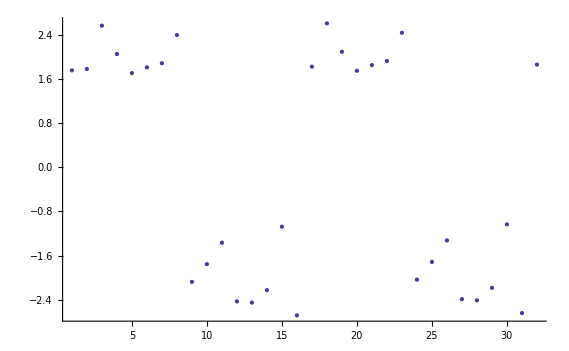

Dot::dotsh: Tensors {-0.21291221905107527`, -0.48495645034991863`, -0.01127680926122919`, « 20 », 0.36977706814458156`, 0.012502896567078217`} and {89.99372162941316`, 44.11683661468369`, 0.8010827713133797`} have incompatible shapes.

7.26252+{-0.212912,-0.484956,-0.0112768,0.209154,0.369777,0.0125029}.{89.9937,44.1168,0.801083}

```mathematica
ListPlot[Table[f[w.X[[j]]],{j,1,32}]]

f[w.Mean[pr]]
```